# Plots for Manuscript

## IGP system with adaptive predator-specific defense and introduced predator

## First replicate Nakazawa by omitting ρ and setting f_i to published values

Define Model

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (-aPR eP fP P+c0 (-1+eP+eΝ) r-aΝR (-1+eΝ) fΝ Ν)

-eP v (aPR (-1+eP) fP P-c0 (-1+eP+eΝ) r+aΝR eΝ fΝ Ν)

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1.,k-> 5., c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1., aΝR -> 1., bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1.};
kpars = Delete[pars, 2]
```

{r→1.,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aPΝ→1.,aΝR→1.,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1.}

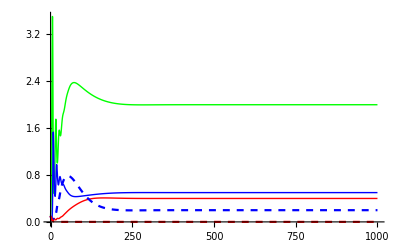

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.pars},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients of k and aPΝ

```mathematica
(*Huzzah! Adaptive predator-specific model works! Not only do the stable/unstable and coexistence dynamics exactly match Nakazawa Fig. 3 but the effort variables  somehow (automatically) sum to less than 1 across all ranges of parameter space (something that I was worried about needing to constrain explicitely)*)
```

```mathematica
kaPΝpars = {r-> 1, c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25,aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1}
```

{r→1,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aΝR→1,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPΝpars,{k->κ,aPΝ->α}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,20},{{α,1,"aPΝ"},0,4}]
```

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[kaPΝpars,{k→5,aPΝ→1}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[kaPΝpars,{k→5,aPΝ→1}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[kaPΝpars,{k→5,aPΝ→1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equilRNP=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,deΝdt == 0,dPdt==0, dePdt==0},{R,Ν, eΝ,P, eP}]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
equil//TableForm
```

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→-(-1+c0) k r | Ν→0 | eΝ→1-eP | P→0 | 
R→k r | Ν→0 | eΝ→0 | P→0 | eP→0
R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→-(-1+c0) k r | Ν→0 | eΝ→1 | P→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→1 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | eΝ→0 | P→(-mP+aPR bPR (-1+c0) (-1+fP) k r)/(aPR^2 bPR (-1+fP)^2 k) | eP→1
R→-(-1+c0) k r | Ν→0 | eΝ→1-1/fP+mP/(aPR bPR fP k r-aPR bPR c0 fP k r) | P→0 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→((-c0+fP) k r)/fP | Ν→0 | eΝ→0 | P→(c0 r)/(aPR fP) | eP→1/fP+mP/(aPR bPR c0 k r-aPR bPR fP k r)
R→(1-(c0 (fP+fΝ))/(fP fΝ)) k r | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aPR fP fΝ mΝ+aPΝ c0 fΝ r+aPR aΝR bΝR (-fP fΝ+c0 (fP+fΝ)) k r)/(aPR aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) k r) | P→(c0 r)/(aPR fP) | eP→(aΝR fP fΝ mP-aPΝ bPΝ c0 fP r+aPR aΝR bPR (-fP fΝ+c0 (fP+fΝ)) k r)/(aPR aΝR bPR fP (-fP fΝ+c0 (fP+fΝ)) k r)
R→(k (aΝR bΝR fΝ (fP+fΝ-fP fΝ) mP+aPR bPR fP (fP+fΝ-fP fΝ) mΝ-aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r))/(aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k) | Ν→(-fP (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPR aΝR bPR bΝR (-1+c0) fP (fP (-1+fΝ)-fΝ) k r)/(aΝR (aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k)) | eΝ→(aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)-aPΝ (aΝR fΝ mP+aPR bPΝ fP mΝ)-aPR aPΝ aΝR (-1+c0) (bPΝ bΝR fP-bPR (-1+fP) fΝ) k r)/(aPR aΝR k ((fP (-1+fΝ)-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r)) | P→-(fΝ (aPR bPR fP mΝ+aΝR bΝR (fΝ mP-aPR bPR (-1+c0) (fP (-1+fΝ)-fΝ) k r)))/(aPR (aPΝ (bPR-bPΝ bΝR) fP fΝ+aPR aΝR bPR bΝR (fP+fΝ-fP fΝ)^2 k)) | eP→(aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (aΝR fΝ mP+aPR bPΝ fP mΝ-aPR aΝR (-1+c0) (bPΝ bΝR fP (-1+fΝ)-bPR fΝ) k r))/(aPR aΝR k ((fP (-1+fΝ)-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)+aPΝ (bPR-bPΝ bΝR) (-1+c0) fP fΝ r))
R→-(k (aΝR mP+aPR bPΝ (-1+fP) mΝ+aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k) | Ν→(-aPR (-1+fP) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)+aPΝ (mP+aPR bPR (-1+c0+fP-c0 fP) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eΝ→0 | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eP→1
R→(aPR fP mΝ+aPΝ c0 r)/(aPR aΝR bΝR fP) | Ν→(-aPR fP mΝ-aPΝ c0 r+aPR aΝR bΝR (-c0+fP) k r)/(aPR aΝR^2 bΝR fP k) | eΝ→0 | P→(c0 r)/(aPR fP) | eP→(aPR fP (-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ))+aPΝ (-aPΝ bPΝ c0+aPR aΝR (bPR c0+bPΝ bΝR (-c0+fP)) k) r)/(aPR aΝR bPR fP k (aPR fP mΝ+aPΝ c0 r))
R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→-(-1+c0) k r | Ν→0 | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | eΝ→1 | P→0 | eP→0
R→-(-1+c0) k r | Ν→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | P→0 | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | P→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→1 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→1
R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
FullSimplify[equil[[17, 2,  2]]]
```

(-mΝ/(bΝR k)+aΝR r)/aΝR^2

```mathematica
equil/.kpars//TableForm
```

Power::infy: Infinite expression 1/0. encountered.

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→0.75 k | Ν→0 | eΝ→1-eP | P→0 | 
R→1. k | Ν→0 | eΝ→0 | P→0 | eP→0
R→(0.1875 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.09375 k)+0.015625 k))/(0.5-0.03125 k) | eΝ→1 | P→(1. (-0.25+0.0625 k))/(0.5-0.03125 k) | eP→0
R→2. | Ν→0.5 | eΝ→(128. (-1. (0.125+0.046875 k)+0.5 (0.5+0.046875 k)))/k | P→(64. (-0.125+0.03125 k))/k | eP→0
R→4. | Ν→0 | eΝ→0 | P→16. (0.25-1./k) | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→1 | P→0 | eP→0
R→4. | Ν→0 | eΝ→1 | P→-(32. (0.5-0.09375 k))/k | eP→0
R→8. | Ν→0 | eΝ→0 | P→(128. (-0.5+0.046875 k))/k | eP→1
R→0.75 k | Ν→0 | eΝ→-1.+10.6667/k | P→0 | eP→2. (1-5.33333/k)
R→0.5 k | Ν→0 | eΝ→0 | P→2. | eP→2.-16./k
R→0. | Ν→0.5 | eΝ→ComplexInfinity | P→2. | eP→ComplexInfinity
R→(0.164063 k)/(0.0625+0.0351563 k) | Ν→(1. (-0.078125+0.0175781 k))/(0.0625+0.0351563 k) | eΝ→-(24.381 (-0.28125+0.00585938 k))/k | P→-(2. (0.03125+0.5 (0.25-0.0703125 k)))/(0.0625+0.0351563 k) | eP→-(24.381 (1. (0.28125-0.0585938 k)+0.0117188 k))/k
R→-(0.09375 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.046875 k)+0.0273438 k))/(0.5-0.03125 k) | eΝ→0 | P→-(1. (0.25+0.03125 k))/(0.5-0.03125 k) | eP→1
R→5. | Ν→(16. (-0.3125+0.03125 k))/k | eΝ→0 | P→2. | eP→(51.2 (0.125 (-0.25-0.1875 k)+1. (-0.125+0.046875 k)))/k
R→1. | Ν→1. (1.-1./k) | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→0.75 k | Ν→0 | eΝ→0 | P→0 | eP→1
R→1. | Ν→-(2. (0.5-0.375 k))/k | eΝ→0 | P→0 | eP→1
R→2. | Ν→(8. (-0.5+0.1875 k))/k | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→2. (1-1.33333/k) | P→0 | eP→-1.+2.66667/k
R→0.5 k | Ν→0.5 | eΝ→2.-4./k | P→0 | eP→0
R→0 | Ν→1. | eΝ→1 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→1
R→(0.0625 k)/(0.5-0.0625 k) | Ν→(1. (1. (0.5-0.125 k)+0.046875 k))/(0.5-0.0625 k) | eΝ→0 | P→(1. (-0.25+0.0625 k))/(0.5-0.0625 k) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
ex = equil[[23, 3, 2]];
Solve[ex==0, k]
```

{{k→(fΝ mΝ)/(aΝR bΝR (-c0+fΝ) r)}}

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν) | -aPR eP eΝ fP v | eΝ (-aPR fP P+c0 r) v
aPR bPR (1-eP fP) P | aPΝ bPΝ P | 0 | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aΝR eP eΝ fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aPR bPR (1-eP fP) P | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν))

```mathematica
mat = JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
mat//MatrixForm
```

(-mΝ/(aΝR bΝR k) | -mΝ/bΝR | (mΝ (-fΝ mΝ+aΝR bΝR (-c0+fΝ) k r))/(aΝR^2 bΝR^2 k)
-mΝ/(aΝR k)+bΝR r | 0 | (fΝ mΝ (mΝ-aΝR bΝR k r))/(aΝR^2 bΝR k)
0 | 0 | (-(fΝ mΝ)/(aΝR bΝR k)+(-c0+fΝ) r) v)

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[pars,2];
```

```mathematica
(* function to substitute equilibrium densities of a given equilibrium into Jacobian. Works. *)
```

```mathematica
Jeq3=J/.equil[[3,All]]//FullSimplify;
Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq6=J/.equil[[6,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq17=J/.equil[[17,All]]//FullSimplify;
Jeq21=J/.equil[[21,All]]//FullSimplify;
Jeq23=J/.equil[[23,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq23RΝ=JRΝ/.equil[[23,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.kpars],#≥0&];
AllFeas4[k_]=AllTrue[Re[equil[[4,All,2]]/.kpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.kpars],#≥0&];
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.kpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.kpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.kpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.kpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.kpars],#≥0&];
AllFeas23[k_]=AllTrue[Re[equil[[23,All,2]]/.kpars],#≥0&];
AllFeas27[k_]=AllTrue[Re[equil[[27,All,2]]/.kpars],#≥0&];
```

```mathematica
AllFeas23[4.5]
```

True

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
pReEig3[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 3]]];
pReEig4[k_]=Max[Re[Eigenvalues[N[Jeq4/.kpars], 3]]];
pReEig5[k_]=Max[Re[Eigenvalues[N[Jeq5/.kpars], 3]]];
pReEig6[k_]=Max[Re[Eigenvalues[N[Jeq6/.kpars], 3]]];
pReEig10[k_]=Max[Re[Eigenvalues[N[Jeq10/.kpars],3]]];
pReEig12[k_]=Max[Re[Eigenvalues[N[Jeq12/.kpars],3]]];
pReEig17[k_]=Max[Re[Eigenvalues[N[Jeq17/.kpars],3]]];
pReEig21[k_]=Max[Re[Eigenvalues[N[Jeq21/.kpars], 3]]];
pReEig23[k_]=Max[Re[Eigenvalues[N[Jeq23/.kpars], 3]]];
pReEig27[k_]=Max[Re[Eigenvalues[N[Jeq27/.kpars], 3]]];
```

```mathematica
(*R system*)
```

```mathematica
pReEig3R[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 1]]];
```

```mathematica
(* RN system *)
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.kpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.kpars]]]];
pReEig23RΝ[k_]=Max[Re[Eigenvalues[N[Jeq23RΝ/.kpars]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.kpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.kpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.kpars]]]];
```

Produce plots

### Abundance-gradient plots (MN)

#### Across k

```mathematica
(* Functions for species-specific equilibria. Gives value of resource for a given k (and IGP strength) at each euilibrium (which can be specified using the double-brackets) *)
pEquilR[k_]=equil[[All,1,2]]/.kpars//FullSimplify
pEquilΝ[k_]=equil[[All,2,2]]/.kpars//FullSimplify;
pEquilP[k_]=equil[[All,4,2]]/.kpars//FullSimplify;
pEquileΝ[k_]=equil[[All,3,2]]/.kpars//FullSimplify;
pEquileP[k_]=equil[[All,5,2]]/.kpars//FullSimplify;
```

{0,0.75 k,1. k,-(6. k)/(-16.+1. k),2.,4.,0,0.75 k,4.,8.,0.75 k,0.5 k,0.,(4.66667 k)/(1.77778+1. k),(3. k)/(-16.+1. k),5.,1.,0,0.75 k,1.,2.,0.75 k,0.5 k,0,0,0,-(1. k)/(-8.+1. k),0}

Power::infy: Infinite expression 1/0. encountered.

Part::partw: Part 5 of {R→0,Ν→0,eΝ→1-eP,P→0} does not exist.

Power::infy: Infinite expression 1/0. encountered.

Part::partw: Part 5 of {R→0,Ν→0,eΝ→1-eP,P→0} does not exist.

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Thin,Green},{Thick,Dashed, Green},{Thin, Blue},{Thick, Dashed,Blue},{Thin,Opacity[0.5, Blue]},{Thick, Dashed,Opacity[0.5, Blue]},
{Thin,Red},{Thick,Dashed,Red}, {Thin,Opacity[0.5, Red]},{Thick,Dashed,Opacity[0.5, Red]}};
```

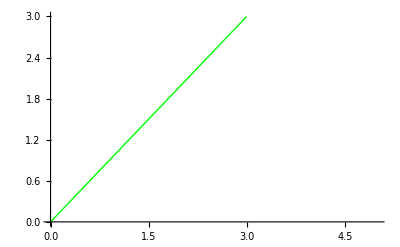

-Graphics-

```mathematica
PlotEqR3=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

```mathematica
PlotEqR17=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
PlotEqR17u=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
```

```mathematica
PlotEqR21=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
PlotEqR21u=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]];
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

```mathematica
PlotEqR23=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];
PlotEqR23u=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

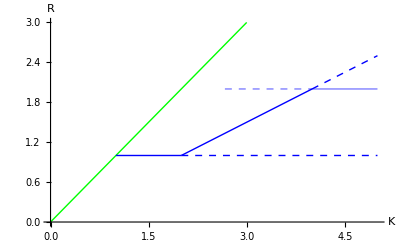

```mathematica
Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR23,PlotEqR23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ23=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0.&&AllFeas23[x]]];
PlotEqΝ23u=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0.&&AllFeas23[x]]];
```

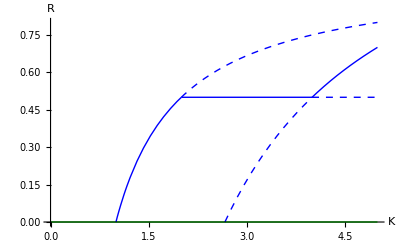

```mathematica
Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ23,PlotEqΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ23=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0&&AllFeas23[x]]];
PlotEqeΝ23u=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

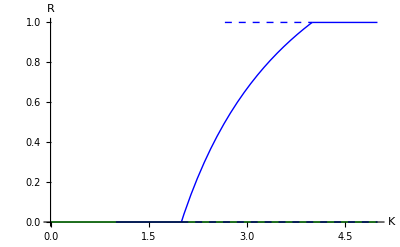

```mathematica
Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ23,PlotEqeΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

#### R-RN-RNP-RP

### Invasibility plot (Fig 2.)

#### One equilibrium at a time

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN23 = equil[[23,1,2]];
NstarRN23= equil[[23,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN23 = bPR aPR (1 -0*fP)RstarRN23  + aPN bPΝ NstarRN23 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝpars
PlotRN17 = Plot[PinvRN17kaPN,{k, 1,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN23 = FullSimplify[Solve[PinvRN23==0,aPN]][[1,1,2]];
PinvRN23kaPN = plotPinvRN23/.kaPΝpars;
PlotRN23 = Plot[PinvRN23kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝpars;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
```

-(0.375 k)/(0.5-0.5 k)

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,4,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,4,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,4,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝpars;
PlotRP6 = Plot[Νinv6kaPN,{k, 4,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝpars;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝpars;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

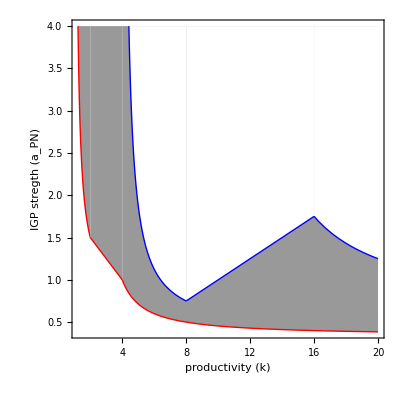

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN23,PlotRP6,PlotRP10, PlotRP12, PlotRange->Automatic, Frame->True,FrameLabel->{"productivity (k)","IGP stregth (a_PN)"}, AspectRatio -> 1/1, LabelStyle -> Larger]
```

## Introduced Top Predator (P): suboptimal defense toward P

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/IGP-adaptive-defense

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fΝ ϕ));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fΝ ϕ) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fΝ ϕ);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (c0 (-1+eP+eΝ) r-fΝ (aΝR (-1+eΝ) Ν+aPR eP P ϕ))

eP v (c0 (-1+eP+eΝ) r-fΝ (aΝR eΝ Ν+aPR (-1+eP) P ϕ))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsM = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.75};
parsL = {r-> 1,k-> 6, c0->0.2, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.5};
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexM = {r-> 1,k-> 6, c0->0.2, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.75};
parsCoexL = {r-> 1,k-> 6, c0->0.2, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.5};
```

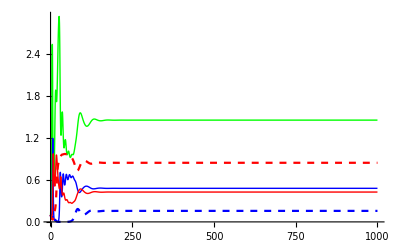

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoexH},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕman = Delete[parsCoexH, 14];
c0parsRN ={r-> 1,k-> 1, fΝ->0.5,  aPR-> 0.1, aPΝ -> 0.1, aΝR -> 0.8, bPΝ->0.1, bΝR->0.8, bPR->0.1, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
```

{r→1,k→1,fΝ→0.5,aPR→0.1,aPΝ→0.1,aΝR→0.8,bPΝ→0.1,bΝR→0.8,bPR→0.1,mP→0.5,mΝ→0.2,v→1,ϕ→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[c0parsRN,{c0 -> χ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{χ,0.5,"c0"},0,1}]
```

Simulation plots

### Final densities of RNP across relative efficiencies of toward P (ϕ)

```mathematica
parsaltϕ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

```mathematica
parsϕ = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1}
```

{r→1,k→5,c0→0.25,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1}

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsaltϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];
finalϕR = Plot[Evaluate[R[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{1,0},{0,3}}];
finalϕΝ = Plot[Evaluate[Ν[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Blue}, 
PlotRange->{{1,0},{0,3}}];
finalϕP = Plot[Evaluate[P[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015], Red}, 
PlotRange->{{1,0},{0,3}}];
finalϕeΝ = Plot[Evaluate[eΝ[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{1,0},{0,3}}];
finalϕeP = Plot[Evaluate[eP[ϕ][500]/.finalϕ,{ϕ,1,0}],PlotStyle-> {Thickness[0.015],Red, Dashed}, 
PlotRange->{{1,0},{0,3}}];
```

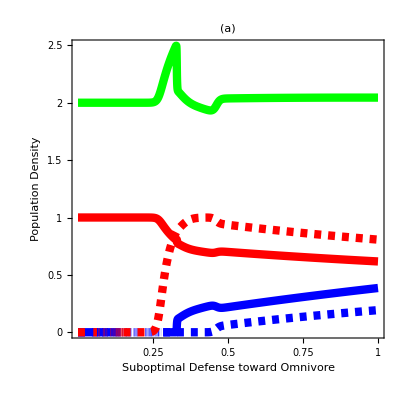

```mathematica
Fig4a = Show[finalϕR,finalϕΝ,finalϕeΝ, finalϕP, finalϕeP,
PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
Frame-> True,FrameLabel->{"Suboptimal Defense toward Omnivore","Population Density", None,"Defense Effort"}, Spacings -> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]
```

### Final densities of RNP across productivity gradient for various levels of ϕ

#### Manipulate across gradient of k

```mathematica
kaPNc0ϕpars = Delete[parsCoexH, {{2},{3},{6}, {14}}]
```

{r→1,fΝ→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPNc0ϕpars,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,10}, {{χ,0.2,"c0"},0,1}, {{α,1.2,"aPΝ"},0,4}, {{Φ,1,"ϕ"},0,1}]
```

```mathematica
kparsϕH = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
kparsϕM = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.75};
kparsϕL = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

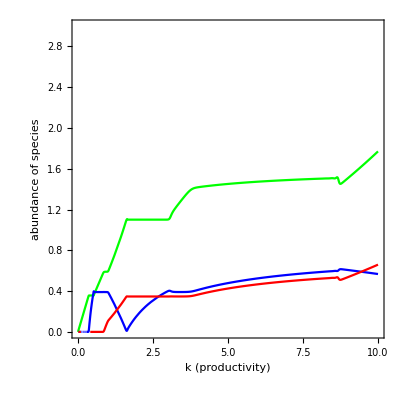

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

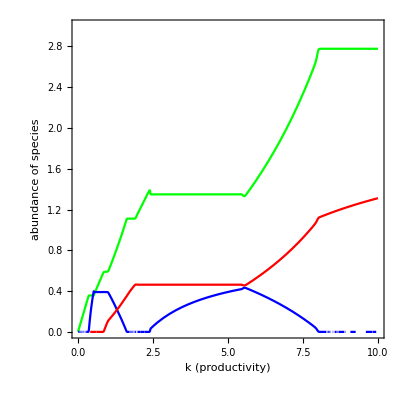

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1, LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

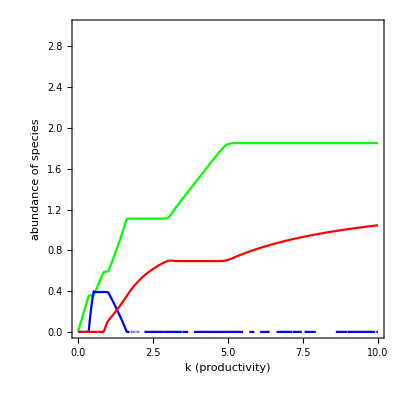

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Plot final densities across a range of c0

```mathematica
c0parsϕH = {r-> 1, k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
c0parsϕM = {r-> 1,  k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.75};
c0parsϕL = {r-> 1, k-> 5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

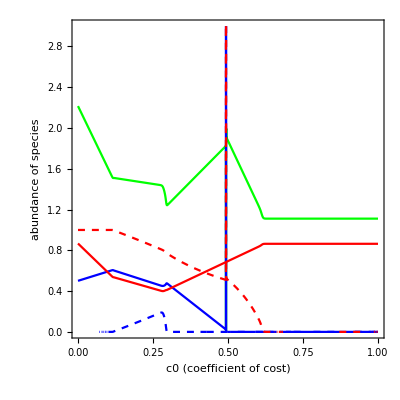

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

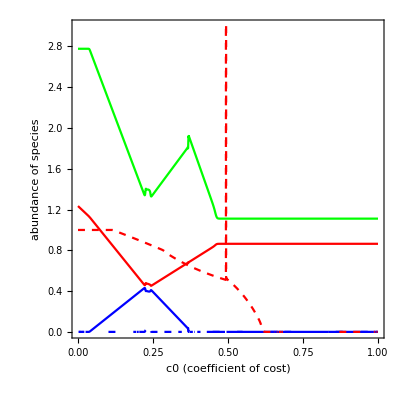

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

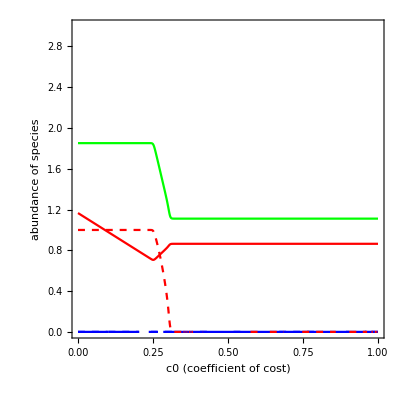

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1 | R→0 | Ν→0 | P→0 | eΝ→1-eP | 
2 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-eP | 
3 | R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
4 | R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | eP→0
5 | R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
6 | R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
7 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
8 | R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
9 | R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
10 | R→-(k (aΝR mP+aPΝ bPΝ (-1+c0) r+aPR bPΝ mΝ (-1+fΝ ϕ)))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ)) | Ν→(-aPR k (-1+fΝ ϕ) (aΝR bΝR mP+aPR bPR mΝ (-1+fΝ ϕ))+aPΝ (mP-aPR bPR (-1+c0) k r (-1+fΝ ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bPΝ bΝR (-1+c0) r+aPR bPR mΝ (-1+fΝ ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ))) | eΝ→0 | eP→1
11 | R→mP/(aPR bPR-aPR bPR fΝ ϕ) | Ν→0 | P→(-mP+aPR bPR (-1+c0) k r (-1+fΝ ϕ))/(aPR^2 bPR k (-1+fΝ ϕ)^2) | eΝ→0 | eP→1
12 | R→-(k r (c0+c0 ϕ-fΝ ϕ))/(fΝ ϕ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→-(aPΝ c0 r+aPR fΝ mΝ ϕ+aPR aΝR bΝR k r (c0+c0 ϕ-fΝ ϕ))/(aPR aΝR bΝR fΝ k r (fΝ ϕ-c0 (1+ϕ))) | eP→(-aΝR fΝ mP ϕ+aPΝ bPΝ c0 r ϕ-aPR aΝR bPR k r (c0+c0 ϕ-fΝ ϕ))/(aPR aΝR bPR fΝ k r ϕ (fΝ ϕ-c0 (1+ϕ)))
13 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-1/(fΝ ϕ)+mP/(aPR bPR fΝ k r ϕ-aPR bPR c0 fΝ k r ϕ) | eP→(mP-aPR bPR k r+aPR bPR c0 k r)/(-aPR bPR fΝ k r ϕ+aPR bPR c0 fΝ k r ϕ)
14 | R→(k (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r ϕ+aΝR bΝR mP (1+ϕ-fΝ ϕ)+aPR bPR mΝ ϕ (1+ϕ-fΝ ϕ)))/(aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2) | Ν→(ϕ (-aPR bPR mΝ ϕ+aΝR bΝR (-mP+aPR bPR (-1+c0) k r (-1+(-1+fΝ) ϕ))))/(aΝR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2)) | P→(-aPR bPR mΝ ϕ+aΝR bΝR (-mP+aPR bPR (-1+c0) k r (-1+(-1+fΝ) ϕ)))/(aPR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2)) | eΝ→(aPR aΝR k (-1+(-1+fΝ) ϕ) (aΝR bΝR mP+aPR bPR mΝ (-1+fΝ ϕ))-aPΝ (aPR bPΝ mΝ ϕ+aΝR (mP+aPR (-1+c0) k r (bPR+bPΝ bΝR ϕ-bPR fΝ ϕ))))/(aPR aΝR fΝ k (aΝR bΝR mP (-1+(-1+fΝ) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (-1+(-1+fΝ) ϕ)))) | eP→(aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-1+(-1+fΝ) ϕ)+aPΝ (aPR bPΝ mΝ ϕ+aΝR (mP+aPR (-1+c0) k r (bPR-bPΝ bΝR (-1+fΝ) ϕ))))/(aPR aΝR fΝ k (aΝR bΝR mP (-1+(-1+fΝ) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (-1+(-1+fΝ) ϕ))))
15 | R→(aPΝ c0 r+aPR fΝ mΝ ϕ)/(aPR aΝR bΝR fΝ ϕ) | Ν→-(aPΝ c0 r+aPR fΝ mΝ ϕ+aPR aΝR bΝR k r (c0-fΝ ϕ))/(aPR aΝR^2 bΝR fΝ k ϕ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→((-aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k)/(aPR aΝR fΝ k ϕ)+(bΝR (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ c0 r+aPR fΝ mΝ ϕ))/bPR
16 | R→k r (1-c0/(fΝ ϕ)) | Ν→0 | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→1/(fΝ ϕ)+mP/(aPR bPR c0 k r-aPR bPR fΝ k r ϕ)
17 | R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
18 | R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
19 | R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | P→0 | eΝ→1 | eP→0
20 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
21 | R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | eP→0
22 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
23 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
24 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
25 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
26 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
27 | R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
28 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

```mathematica
(* Only takes a few seconds, just like the Nakazawa formulation (not surprisingly). What is surprising is how much longer the ρ equil takes. I guess that manipulating the replicator equation is qualitatively different than adding a parameter *)
```

```mathematica
thresh19N =equil[[19, 2,2]]
```

(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k)

```mathematica
cost19 =FullSimplify[Solve[thresh19N==0,c0]]
```

{{c0→1-mΝ/(aΝR bΝR k r-aΝR bΝR fΝ k r)}}

```mathematica
Νinv9kaPN = plotΝinv9/.c0aPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,
PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9M[x]]];
```

ReplaceAll::reps: {c0aPΝparsH} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
thresh21N =equil[[21, 2,2]]
```

(c0 r)/(aΝR fΝ)

```mathematica
thresh21R =equil[[21, 1,2]]
```

((-c0+fΝ) k r)/fΝ

```mathematica
Solve[thresh21N==0,c0]
```

{{c0→0}}

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]/.{eP-> 0, P-> 0}//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]/.{eΝ-> 0, Ν -> 0}//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν+aPR P (-1+eP fΝ ϕ) | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | aPR R (-1+eP fΝ ϕ) | R (-c0 r+aPR fΝ P ϕ)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (c0 (-1+eP+2 eΝ) r+aΝR fΝ (Ν-2 eΝ Ν)-aPR eP fΝ P ϕ) | -aPR eP eΝ fΝ v ϕ | eΝ v (c0 r-aPR fΝ P ϕ)
aPR bPR P (1-eP fΝ ϕ) | aPΝ bPΝ P | 0 | -mP+aPΝ bPΝ Ν+aPR bPR R (1-eP fΝ ϕ) | -aPR bPR fΝ P R ϕ
0 | -aΝR eP eΝ fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (-1+eP) eP fΝ v ϕ | v (c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν+aPR (1-2 eP) fΝ P ϕ))

(r-c0 eΝ r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v | (-1+2 eΝ) v (c0 r-aΝR fΝ Ν))

(r-c0 eP r-(2 R)/k+aPR P (-1+eP fΝ ϕ) | aPR R (-1+eP fΝ ϕ) | R (-c0 r+aPR fΝ P ϕ)
aPR bPR P (1-eP fΝ ϕ) | -mP+aPR bPR R (1-eP fΝ ϕ) | -aPR bPR fΝ P R ϕ
0 | -aPR (-1+eP) eP fΝ v ϕ | (-1+2 eP) v (c0 r-aPR fΝ P ϕ))

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
subpars=Delete[parsCoexH,3];
subparsM=Delete[parsCoexM,3];
subparsL=Delete[parsCoexL,3];
```

```mathematica
(*R system*)
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas9[c0_]=AllTrue[Re[equil[[9,All,2]]/.subpars],#≥0&];
AllFeas11[c0_]=AllTrue[Re[equil[[11,All,2]]/.subpars],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];

AllFeas9M[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.subpars]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];

pReEig17RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subpars]]]];
pReEig16RP[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subpars]]]];
pReEig11RP[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subpars]]]];

pReEig9RPM[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsCoexH, {{3},{6}}];
c0aPΝparsM = Delete[parsCoexM, {{3},{6}}];
c0aPΝparsL = Delete[parsCoexL, {{3},{6}}];
```

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

-mP+(aPR bPR mΝ)/(aΝR bΝR)+(aPN bPΝ (-mΝ/(bΝR k)+aΝR r))/aΝR^2

-mP+(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR (-c0+fΝ) k r)/fΝ

-mP+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)+(aPN bPΝ (-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r))/(aΝR^2 bΝR (-1+fΝ)^2 k)

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = FullSimplify[bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ]
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPR^2 bPR k)

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ
```

(aΝR bΝR mP)/(aPR bPR)-mΝ-(aPΝ (-mP/(bPR k)+aPR r))/aPR^2

-mΝ+aΝR bΝR k r (1-c0/(fΝ ϕ))-(aPΝ c0 r)/(aPR fΝ ϕ)

-mΝ+(aΝR bΝR mP)/(aPR bPR-aPR bPR fΝ ϕ)-(aPΝ (-mP+aPR bPR (-1+c0) k r (-1+fΝ ϕ)))/(aPR^2 bPR k (-1+fΝ ϕ)^2)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]]
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ))/(-mP+aPR bPR k r)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,k]][[1,1,2]]
```

(aPΝ mP)/(aPR (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPR r))

-Graphics-

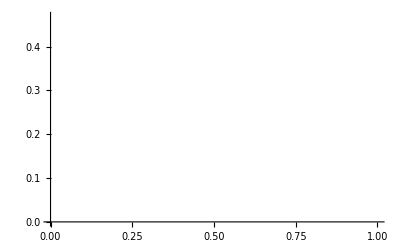

-Graphics-

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,
PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]]

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]]

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]]
```

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig3a =Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21, PlotRN17a, PlotRN21a,PlotRN19,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.8}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1",FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}}, 
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.8],
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];
```

```mathematica
Fig3b = Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21,PlotRN17a, PlotRN21a,PlotRN19, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.25}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(b)    ϕ = 0.75",FontSize->14,  Bold], 
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Low relative efficiency (ϕ = 0.5)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,40}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];

(*p invades*)

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1},  PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN - 0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White,
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];
```

```mathematica
Fig3c= Show[PlotRP9,PlotRP16, PlotRP11,PlotRN17, PlotRN21,PlotRN17a,PlotRN21a,PlotRN19,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True,AspectRatio -> 1/1, 
PlotRange->{{0,1},{0,2}},
FrameTicks->{{{1,2},{None}},{{None}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

```mathematica
Figure3abc = Panel[GraphicsRow[{Fig3a,Fig3b,Fig3c}, ImageSize-> 432], {"cost of defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-cost of defenseIGP strength

```mathematica
Figure3abcDIS = Panel[GraphicsRow[{Fig3a,Fig3b,Fig3c}, ImageSize-> 414], {"cost of defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-cost of defenseIGP strength

```mathematica
Export["Figs/MoNSTR_Fig3abc.pdf",Figure3abcDIS]
```

Figs/MoNSTR_Fig3abc.pdf

Produce Plots across k

## Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9[k_]=AllTrue[Re[equil[[9,All,2]]/.subpars],#≥0&];
AllFeas11[k_]=AllTrue[Re[equil[[11,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];

AllFeas9M[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];

pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subpars]]]];
pReEig16RP[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subpars]]]];
pReEig11RP[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subpars]]]];

pReEig9RPM[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{6}}];
kaPΝparsM = Delete[parsCoexM, {{2},{6}}];
kaPΝparsL = Delete[parsCoexL, {{2},{6}}];
```

#### new

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

-mP+(aPR bPR mΝ)/(aΝR bΝR)+(aPN bPΝ (-mΝ/(bΝR k)+aΝR r))/aΝR^2

-mP+(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR (-c0+fΝ) k r)/fΝ

-mP+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)+(aPN bPΝ (-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r))/(aΝR^2 bΝR (-1+fΝ)^2 k)

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.kaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> {White},  
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.kaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.kaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];
```

```mathematica
Fig2a = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.05}]]}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.05,0.02}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.85,0.9}],Scaled[{0.98,0.9}]}]}],PlotLabel -> Style["ϕ = 1, ρ = 1", FontSize->12,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

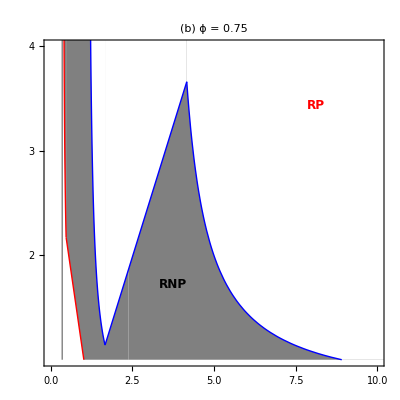

```mathematica
Fig2b = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.38,0.25}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{1,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];
```

```mathematica
Fig2c = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.3,0.35}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.25,0.28}],Scaled[{0.1,0.11}]}]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.3,0.28}],Scaled[{0.36,0.04}]}]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

```mathematica
Figure2abc = Panel[GraphicsRow[{Fig2a,Fig2b,Fig2c}, ImageSize-> 432, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

-Graphics-productivity (k)IGP strength

```mathematica
Export["Figs/MoNSTR_Fig2abc.pdf",Figure2abc]
```

Figs/MoNSTR_Fig2abc.pdf

Multipanel of resource and single predator across c0

```mathematica
c0parsRN ={r-> 1,k-> 1, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1, aΝR -> 1.5, bPΝ->0.5, bΝR->0.8, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
```

{r→1,k→1,fΝ→0.8,aPR→0.9,aPΝ→1,aΝR→1.5,bPΝ→0.5,bΝR→0.8,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→1}

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
pEquilR[c0_]=equil[[All,1,2]]/.c0parsRN//FullSimplify;
pEquilΝ[c0_]=equil[[All,2,2]]/.c0parsRN//FullSimplify;
pEquileΝ[c0_]=equil[[All,4,2]]/.c0parsRN//FullSimplify;
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.c0parsRN],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.c0parsRN],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.c0parsRN],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.c0parsRN],#≥0&];
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.c0parsRN]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.c0parsRN]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.c0parsRN]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.c0parsRN]]]];
```

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Green, Thickness[0.015]},{Thickness[0.005],Dashed, Opacity[0.5, Green]},{Thickness[0.015], Blue},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},{Thickness[0.005],Opacity[0.5, Blue]},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},
{Thickness[0.015],Red},{Thickness[0.005],Dashed,Opacity[0.5, Red]}, {Thickness[0.015],Opacity[0.5, Red]},{Thickness[0.005],Dashed,Opacity[0.5, Red]},  {Thickness[0.015],Purple},  {Thickness[0.005],Dashed,Opacity[0.5, Purple]}, {Thickness[0.005],Dashed, Opacity[0.5, Black] }};
```

-Graphics-

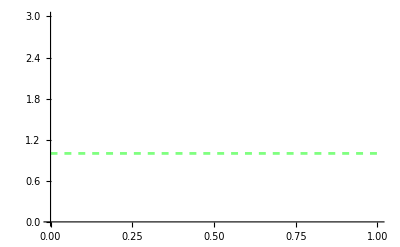

```mathematica
PlotEqR3=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

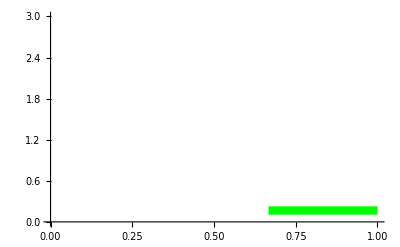

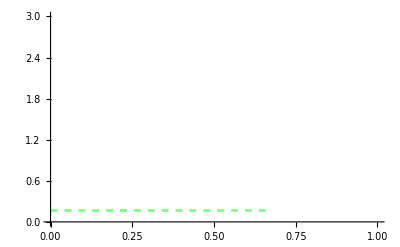

```mathematica
PlotEqR17=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]]
PlotEqR17u=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]]
```

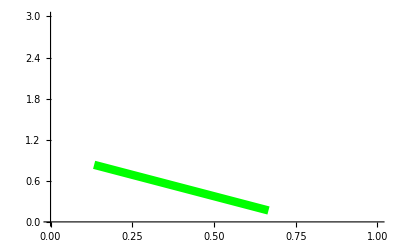

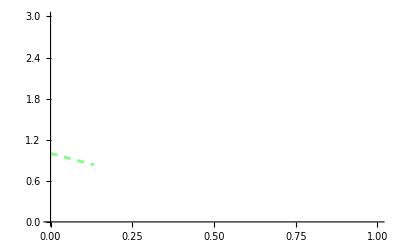

```mathematica
PlotEqR21=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]]
PlotEqR21u=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]]
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

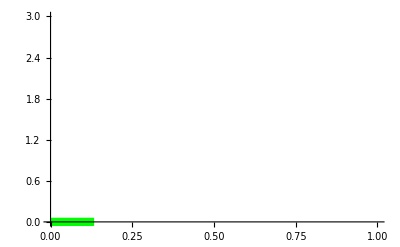

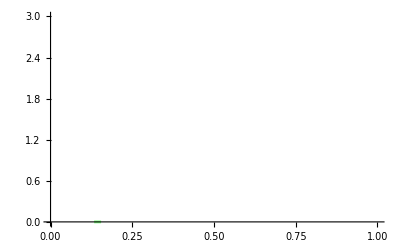

```mathematica
PlotEqR19=Plot[{pEquilR[c0][[23]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]]
PlotEqR19u=Plot[{pEquilR[c0][[23]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]]
```

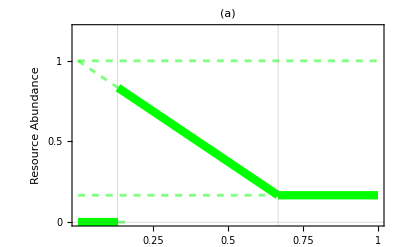

```mathematica
Fig1a = Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR19,PlotEqR19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(a)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},LabelStyle->{Black, Larger},Spacings-> 30,
FrameLabel->{None,"Resource Abundance"},Frame->True,RotateLabel->True]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ19=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0.&&AllFeas19[x]]];
PlotEqΝ19u=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0.&&AllFeas19[x]]];
```

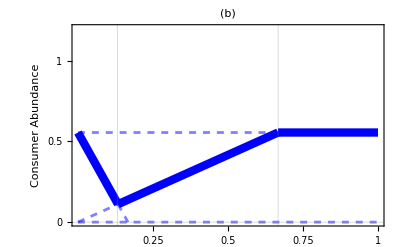

```mathematica
Fig1b = Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ19,PlotEqΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(b)                                                                                 ",  FontSize->14,  Bold],
GridLines -> {{0.132, 0.667}, {0}},
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
FrameLabel->{None,"Consumer Abundance"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ19=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0&&AllFeas19[x]]];
PlotEqeΝ19u=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]];
```

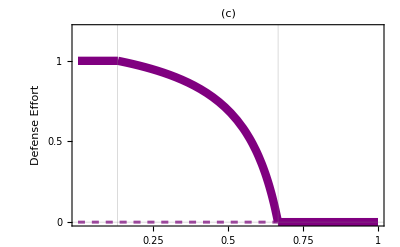

```mathematica
Fig1c = Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ19,PlotEqeΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(c)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},
FrameLabel->{None,"Defense Effort"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]
```

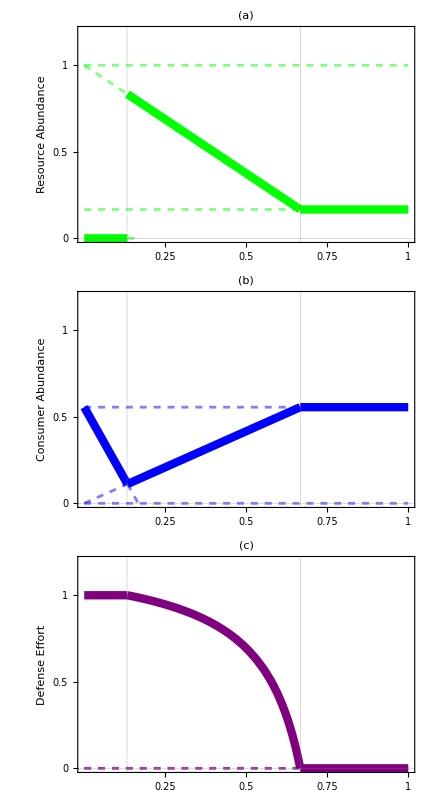
-Graphics-Cost of Defense

```mathematica
Figure1abc = Panel[GraphicsColumn[{Fig1a,Fig1b,Fig1c},  ImageSize-> 432, Spacings->0], {"Cost of Defense",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger];
Figure1abcDIS = Panel[GraphicsColumn[{Fig1a,Fig1b,Fig1c},  ImageSize-> 432, Spacings->0], {"Cost of Defense",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger]
```

```mathematica
Export["Figs/MoNSTR_Fig1_Full.pdf",Figure1abc]
Export["Figs/MoNSTR_Fig1_Full.tiff",Figure1abcDIS, ImageResolution->600]
```

Figs/MoNSTR_Fig1_Full.pdf

Figs/MoNSTR_Fig1_Full.tiff

## Plot ϕ against IGP strength (not useful)

### Functions for working with equilibrium values across a gradient of productivity (ϕ)

```mathematica
parsCoexc0L = {r-> 1,k-> 6, c0->0.1, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexc0M = {r-> 1,k-> 6, c0->0.3, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexc0H = {r-> 1,k-> 6, c0->0.5, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
```

```mathematica
subparsL=Delete[parsCoexc0L,14];
subparsM=Delete[parsCoexc0M,14];
subparsH=Delete[parsCoexc0H,14];
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9L[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];

AllFeas9M[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9H[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsH],#≥0&];
AllFeas11H[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsH],#≥0&];
AllFeas16H[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];
AllFeas17H[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19H[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];
AllFeas21H[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];
```

```mathematica
pReEig17RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];

pReEig17RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]]; 
pReEig21RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig19RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];
```

```mathematica
pReEig9RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];

pReEig9RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsH]]]];
pReEig16RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsH]]]];
pReEig11RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsH]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
ϕaPΝparsL = Delete[parsCoexc0L, {{6},{14}}];
ϕaPΝparsM = Delete[parsCoexc0M, {{6},{14}}];
ϕaPΝparsH = Delete[parsCoexc0H, {{6},{14}}];
```

#### new

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

(aΝR k (-aΝR bΝR mP+aPR bPR mΝ))/(bPΝ (mΝ-aΝR bΝR k r))

0.577215

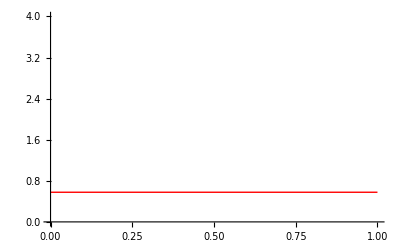

(aΝR fΝ mP+aPR aΝR bPR (c0-fΝ) k r)/(bPΝ c0 r)

-23.84

-Graphics-

-Graphics-

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]]
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsL
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]


plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]]
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsL
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

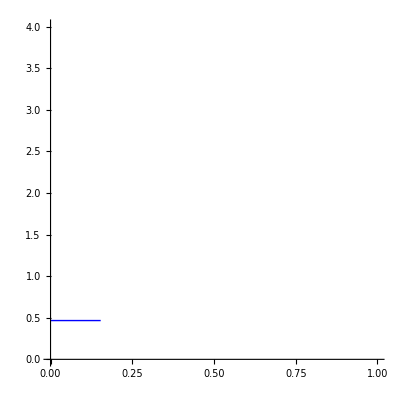

-Graphics-

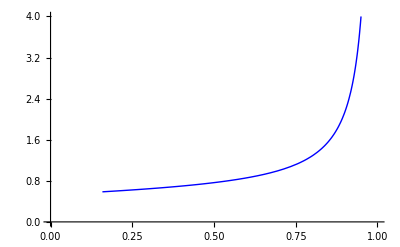

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]]

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig16RPL[x]< 0&&AllFeas16L[x]]]

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]]
```

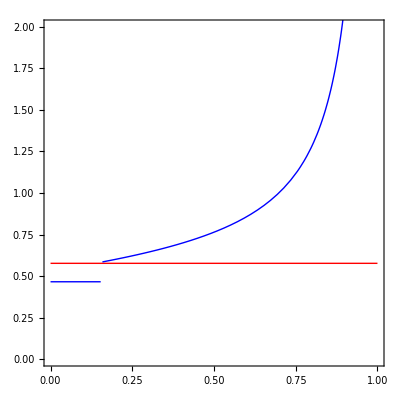

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

#### Medium cost (c0 = 0.5)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

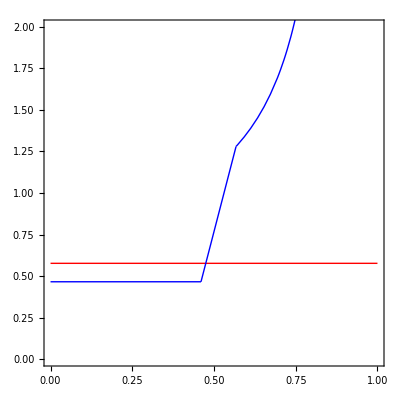

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

#### High cost (c0 = 0.75)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPH[x]< 0&&AllFeas9H[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPH[x]<0&&AllFeas16H[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPH[x]<0&&AllFeas11H[x]]];
```

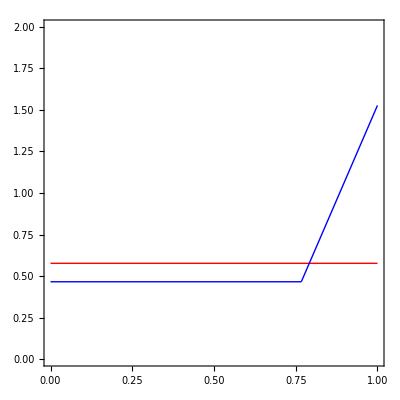

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

## Introduced Top Predator (P): naivete toward P

Define Model

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) - (1-ρ) aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.2, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
```

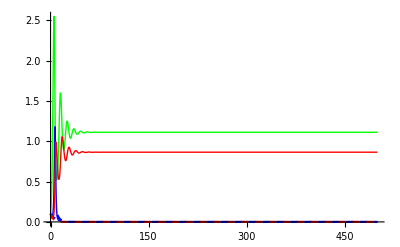

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoex},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients of ρ

```mathematica
parsρ = {r-> 1,k-> 5, c0->0.15, fΝ->0.8,  fP->0.8,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1};
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsρ,{ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,10000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Ρ,0.5,"ρ"},0,1}]
```

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {{R'[t]==R[t] (r Plus[«2»]-aPR Plus[«2»] P[«1»]-Power[«2»] R[«1»]-aΝR Plus[«2»] Ν[«1»]),R[0]==0.1},{Ν'[t]==(-mΝ-aPΝ P[«1»]+aΝR bΝR Plus[«2»] R[«1»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (-mP+aPR bPR Plus[«2»] R[«1»]+aPΝ bPΝ Ν[«1»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (c0 r Plus[«3»]-aPR fP eP[«1»] P[«1»]-aΝR fΝ Plus[«2»] Ν[«1»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (-c0 r Plus[«3»]+aPR fP Plus[«2»] P[«1»]+aΝR fΝ eΝ[«1»] Ν[«1»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}] in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsρ,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kparsρH = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
kparsρM = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
kparsρL = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝH = Plot[Evaluate[eΝ[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePH = Plot[Evaluate[eP[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝM = Plot[Evaluate[eΝ[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePM = Plot[Evaluate[eP[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝL = Plot[Evaluate[eΝ[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePL= Plot[Evaluate[eP[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

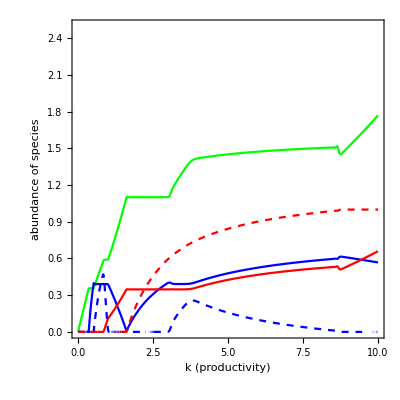

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,kfinaleΝH, kfinalePH, Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

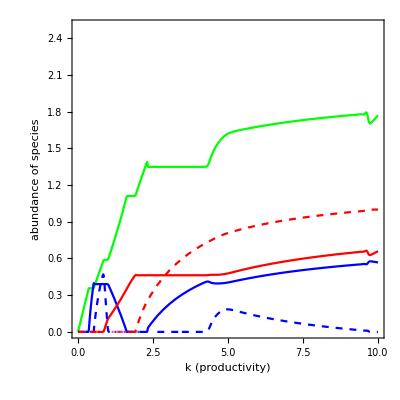

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,kfinaleΝM, kfinalePM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

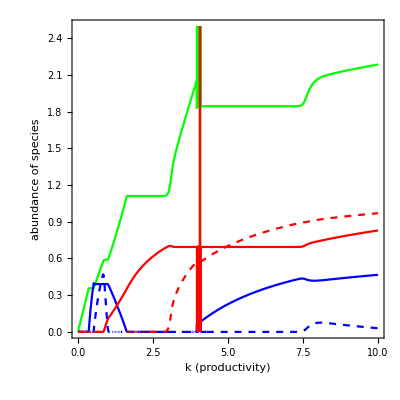

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,kfinaleΝL, kfinalePL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Final Densities across cost

```mathematica
c0parsρH = {r-> 1, k->5, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
c0parsρM = {r-> 1, k->5, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
c0parsρL = {r-> 1, k->5, fΝ->0.8,fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρH},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePL= Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

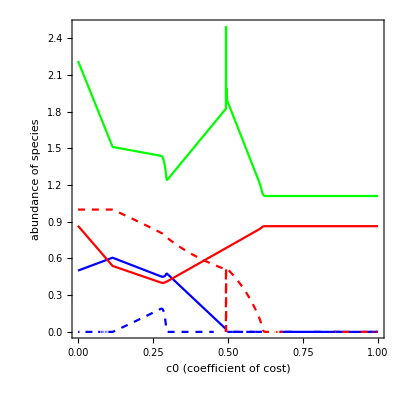

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

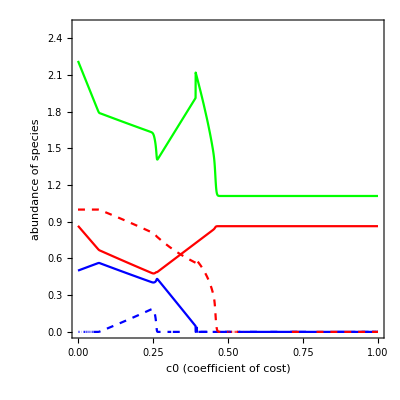

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePM, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

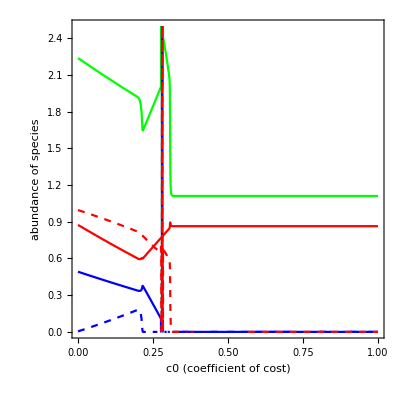

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Final densities of RNP across relative efficiencies of toward P (ρ)

```mathematica
parsStabρ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabρ},{R,Ν, P, eΝ, eP},{t,0,10000}, {ρ}];
finalρR = Plot[Evaluate[R[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{0,1},{0,3}}];
finalρΝ = Plot[Evaluate[Ν[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Blue},
PlotRange->{{0,1},{0,3}}];
finalρP = Plot[Evaluate[P[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Red},
PlotRange->{{0,1},{0,3}}];
finalρeΝ = Plot[Evaluate[eΝ[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle->{Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
finalρeP = Plot[Evaluate[eP[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015],Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

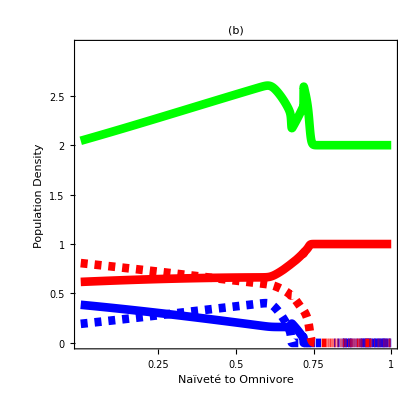

```mathematica
Fig4b =Show[finalρR,finalρΝ,finalρeΝ, finalρP, finalρeP,Frame-> True, FrameLabel->{"Naïveté to Omnivore","Population Density", "","Defense Effort"}, 
PlotLabel -> Style["(b)                                                                                       ", FontSize->14,  Bold],
ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, FontSize-> 11};
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]
```

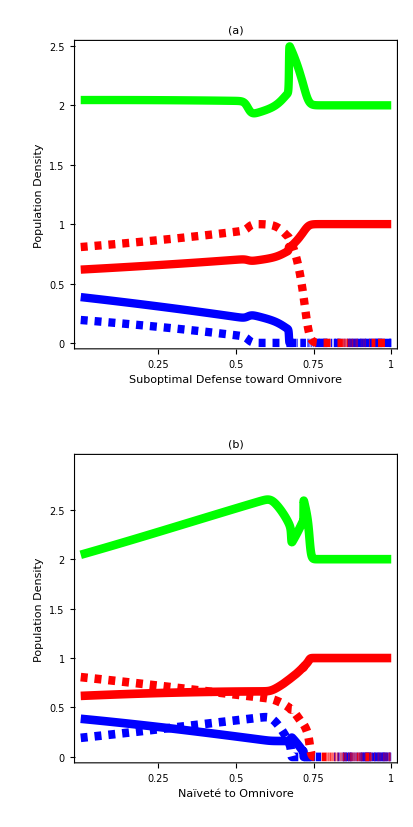
-Graphics-Novelty Gradient

```mathematica
Fig2ab =  Panel[GraphicsColumn[{Fig4a,Fig4b}, ImageSize-> 216, Spacings->{0,0}], 
{"Novelty Gradient",Rotate["Population Density / Defense Effort",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Larger];
Fig4ab =  Panel[GraphicsColumn[{Fig4a,Fig4b}, ImageSize-> 414, Spacings->0], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
```

```mathematica
Export["Figs/MoNSTR_Fig4_Full.tiff",Fig4ab,"TIFF", ImageResolution-> 600]
```

Solve for equilibria

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1-eP | 
R→0 | Ν→0 | P→0 | eΝ→1-eP | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aΝR aPR bPR k r (fΝ-c0))/(aΝR aPR^2 bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ r (aPΝ bPΝ c0+aΝR aPR k (bΝR bPΝ c0+bPR (fΝ-c0))))/(aΝR aPR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→-(-(√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→-((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)-c0 (ρ-2)-fP ρ)/(2 c0 fP (ρ-1))
R→-((√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)+c0 (ρ-2)+fP ρ)/(2 c0 fP (ρ-1))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bΝR bPΝ ρ-bPR) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bPR-bΝR bPΝ ρ) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))))))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP)))-aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→-(aΝR aPR^2 bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP))-2 aΝR bΝR fΝ fP mP (ρ-1))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)-√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→(aΝR (-aPR^2) bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (2 aΝR bΝR fΝ fP mP (ρ-1)-aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP)))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ ρ)/(aΝR aPR bΝR fP ρ) | Ν→(-aPΝ^2 bPR c0^2 r^2+aPR fP ρ (aΝR bΝR k r (aΝR bΝR c0 mP (ρ-1)+aPR bPR mΝ ρ (fP-c0))-aPR bPR fP mΝ^2 ρ)+aPΝ aPR bPR c0 ρ r (aΝR bΝR k r (fP-c0)-2 fP mΝ))/(aΝR^2 aPR bΝR fP k ρ (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ)) | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(aPR fP ρ (aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)-aPΝ c0 r (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)))/(aΝR aPR fP k (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→(k r (fΝ-c0))/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r)+1/fΝ | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm;
JRΝ//MatrixForm;
JRP//MatrixForm;
```

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.99};
parsCoexM = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
parsCoexL = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq20RΝ=JRΝ/.equil[[20,All]]//FullSimplify;
Jeq24RΝ=JRΝ/.equil[[24,All]]//FullSimplify;
Jeq22RΝ=JRΝ/.equil[[22,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.subpars],#≥0&];
AllFeas20[k_]=AllTrue[Re[equil[[20,All,2]]/.subpars],#≥0&];
AllFeas22[k_]=AllTrue[Re[equil[[22,All,2]]/.subpars],#≥0&];
AllFeas24[k_]=AllTrue[Re[equil[[24,All,2]]/.subpars],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig20RΝ[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subpars]]]]; 
pReEig24RΝ[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subpars]]]];
pReEig22RΝ[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subpars]]]];

pReEig20RΝM[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{7}}];
kaPΝparsM = Delete[parsCoexM, {{2},{7}}];
kaPΝparsL = Delete[parsCoexL, {{2},{7}}];
```

#### new

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP;
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.kaPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.kaPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.kaPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig2aa = Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.22,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.05}]]}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.05,0.02}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.8,0.9}],Scaled[{0.96,0.9}]}]}],PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],Frame->True, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{None}, {None}}}]
```

-Graphics-

#### Medium naivete (ρ = 0.75)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];
```

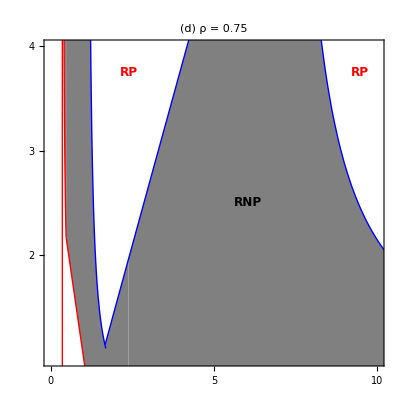

```mathematica
Fig2d=Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.6,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},FrameTicks->{{{2,3, 4},{None}},{{0, 5, 10}, {None}}}]
```

#### Low relative efficiency (ρ = 0.5)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsL;
PlotRN20L = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsL;
PlotRN24L = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsL;
PlotRN22L = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsL;
PlotRP12L = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];
```

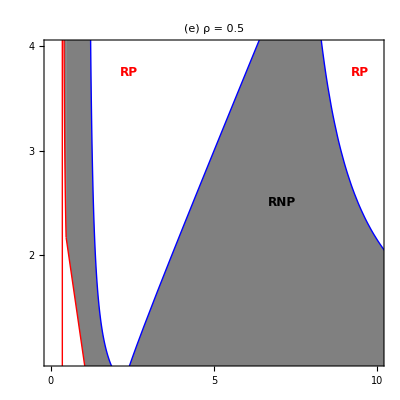

```mathematica
Fig2e =Show[PlotRN20L, PlotRN24L,PlotRN22L,PlotRP6L,PlotRP12L, PlotRP10L,Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]}],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold], 
FrameTicks->{{{2,3, 4},{None}},{{0, 5, 10}, {None}}}]
```

```mathematica
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.225}]}]}],
```

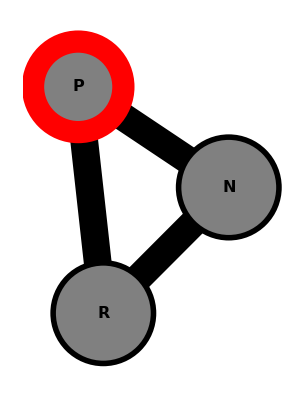

```mathematica
igpO=
Show[
Graphics[{{GrayLevel[0],Thickness[0.05],
Line[{{0.1, 0.1},{.6,.6}}], 
Line[{{0.6, 0.6},{0,1}}], 
Line[{{0.1, 0.1},{0,1}}] 
}}],
Graphics[{{GrayLevel[0.5],Disk[{.1,.1},.2]},{GrayLevel[0.5], Disk[{.6,.6},.2]}, {GrayLevel[0.5],Disk[{0,1.0},.2]}, {Red,Thickness[0.04],Circle[{0,1.0},.18]}, 
{Black,Thickness[0.01],Circle[{0.1,0.1},.2]}, 
{Black,Thickness[0.01],Circle[{0.6,0.6},.2]}}],
Graphics[{Text[Style["R",16,Black , Bold],{0.1,0.1}], 
Text[Style["N",16,Black , Bold],{0.6,0.6}],
Text[Style["P",16,Black , Bold],{0,1}]}]]
```

```mathematica
Figure2abcde = Panel[GraphicsGrid[{{Fig2aa,Fig2b, Fig2c},{igpO, Fig2d, Fig2e}}, ImageSize-> 518, Spacings->{0,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-ProductivityIGP strength

```mathematica
Figure2abcdeDIS = Panel[GraphicsGrid[{{Fig2aa,Fig2b, Fig2c},{igpO, Fig2d, Fig2e}}, ImageSize-> 414, Spacings->{0,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-ProductivityIGP strength

```mathematica
(* Export["Figs/MoNSTR_Fig2_Full.tiff",Figure2abcdeDIS,"TIFF", ImageResolution->600] *)
```

```mathematica
Export["MoNSTR_Fig2_Full.pdf",Figure2abcde]
```

MoNSTR_Fig2_Full.pdf

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.99};
parsCoexM = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
parsCoexL = {r-> 1,k-> 5, c0->0.2, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
subpars=Delete[parsCoexH,3];
subparsM=Delete[parsCoexM,3];
subparsL=Delete[parsCoexL,3];
```

```mathematica
AllFeas6[c0_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas10[c0_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas12[c0_]=AllTrue[Re[equil[[12,All,2]]/.subpars],#≥0&];
AllFeas20[c0_]=AllTrue[Re[equil[[20,All,2]]/.subpars],#≥0&];
AllFeas22[c0_]=AllTrue[Re[equil[[22,All,2]]/.subpars],#≥0&];
AllFeas24[c0_]=AllTrue[Re[equil[[24,All,2]]/.subpars],#≥0&];

AllFeas6M[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig20RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subpars]]]]; 
pReEig24RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subpars]]]];
pReEig22RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subpars]]]];

pReEig20RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig12RP[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subpars]]]];
pReEig10RP[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];

pReEig6RPM[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsCoexH, {{3},{7}}];
c0aPΝparsM = Delete[parsCoexM, {{3},{7}}];
c0aPΝparsL = Delete[parsCoexL, {{3},{7}}];
```

### Invasibility Plot (k and aPN)

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

(aPΝ bPΝ (aΝR r-mΝ/(bΝR k)))/aΝR^2+(aPR bPR mΝ)/(aΝR bΝR)-mP

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]]
Νinv6kaPN = plotΝinv6/.c0aPΝparsH
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]]
Νinv10kaPN = plotΝinv10/.c0aPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

(aPR k (aΝR bΝR mP-aPR bPR mΝ))/(aPR bPR k r-mP)

0.488571

-(aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPR bPR (c0-1) (fP-1) k r-mP)

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig3aa = Show[PlotRP6,PlotRP12, PlotRP10,PlotRN20, PlotRN24,PlotRN22, Frame->True, AspectRatio -> 1/1];
```

#### Medium recognition (ρ = 0.75)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];
```

```mathematica
Fig3d =Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24,PlotRN20a, PlotRN24a,PlotRN22,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold], 
FrameTicks->{{{ 1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

#### Low recognition (ρ = 0.5)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsL
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsL;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsL;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsL;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsL;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsL;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];
```

0.488571

```mathematica
Fig3e=Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24, PlotRN20a, PlotRN24a,PlotRN22,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Graphics[{Blue,Thick,
Line[{{0.3217,0.72},{0.3217,0.49}}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(e)    ρ = 0.5",FontSize->14,  Bold], 
FrameTicks->{{{ 1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
```

-Graphics-

```mathematica
Figure3abcde = Panel[GraphicsGrid[{{Fig3a,Fig3b, Fig3c},{igpO, Fig3d, Fig3e}}, ImageSize-> 518, Spacings->{0,20}], {"Cost of Defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-Cost of DefenseIGP strength

```mathematica
Figure3abcdeDIS = Panel[GraphicsGrid[{{Fig3a,Fig3b, Fig3c},{igpO, Fig3d, Fig3e}}, ImageSize-> 414, Spacings->{0,20}], {"Cost of Defense",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

-Graphics-Cost of DefenseIGP strength

```mathematica
(* Export["Figs/MoNSTR_Fig3_Full.tiff",Figure3abcdeDIS,"TIFF", ImageResolution->600] *)
```

```mathematica
Export["Figs/MoNSTR_Fig3_Full.pdf",Figure3abcde]
```

MoNSTR_Fig3_Full.pdf

## Introduced Intermediate Consumer (Ν): suboptimal defense toward Ν

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fP (1-ϕ))- aPR P (1 - eP fP ));
dΝdt = Ν (bΝR aΝR (1- eΝ fP (1-ϕ)) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fP (1-ϕ)) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (aΝR (eΝ-1) fP Ν (ϕ-1)-aPR eP fP P+c0 r (eΝ+eP-1))

-eP v (-aΝR eΝ fP Ν (ϕ-1)+aPR (eP-1) fP P-c0 r (eΝ+eP-1))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fP->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fP->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsExc = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
parsExcM = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.75};
parsExcL = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.49};

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ϕ->1};
parsFacN = {r-> 1,k-> 0.28, c0->0.15, fP->0.8,  aPR-> 0.9, aPΝ -> 1.5, aΝR -> 0.8, bPΝ->0.5, bΝR->1, bPR->0.5, mP->0.3, mΝ->0.1, v-> 1, ϕ->1};
```

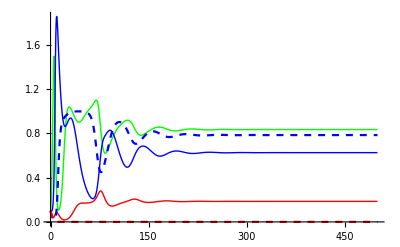

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExc},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕExc = Delete[parsExc, 14]
```

{r→1,k→2.5,c0→0.4,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsϕExc,{ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Φ,1,"ϕ"},0,1}];
```

#### Manipulate across gradient of k and others

```mathematica
parsGood =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 1}
parsϕkaPΝc0 = Delete[parsGood, {{2}, {3},{6},{9},{11}, {14}}];
parsfacminus = Delete[parsFacN, {{2}, {3},{6},{9},{11}, {14}}];
```

{r→1,k→3,c0→0.1,fP→0.6,aPR→1,aPΝ→0.8,aΝR→0.8,bPΝ→0.5,bΝR→0.9,bPR→0.4,mP→0.55,mΝ→0.1,v→1,ϕ→1}

```mathematica
parsFacN
```

{r→1,k→0.28,c0→0.15,fP→0.8,aPR→0.9,aPΝ→1.5,aΝR→0.8,bPΝ→0.5,bΝR→1,bPR→0.5,mP→0.3,mΝ→0.1,v→1,ϕ→1}

```mathematica
{r->1,k->0.28,c0->0.15,fP->0.8,aPR->0.9,aPΝ->1.5,aΝR->0.8,bPΝ->0.5,bΝR->1,bPR->0.5,mP->0.3,mΝ->0.1,v->1,ϕ->1}
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsfacminus,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ, bΝR-> β, mP-> μ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,0.28,"k"},0,10}, {{χ,0.15,"c0"},0,1},{{α,1.5,"aPΝ"},0,2}, 
{{β,1,"bΝR"},0,1}, {{μ,.3,"mP"},0,1},{{Φ,1,"ϕ"},0,1}];
```

#### Comparison Plots

```mathematica
(*exclusion of P with increased novelty*)
```

```mathematica
parsExcPϕ = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1};
```

```mathematica
parsGoodϕ = Delete[parsGood, {14}]
```

{r→1,k→3,c0→0.1,fP→0.6,aPR→1,aPΝ→0.8,aΝR→0.8,bPΝ→0.5,bΝR→0.9,bPR→0.4,mP→0.55,mΝ→0.1,v→1}

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsGoodϕ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ϕ}];
```

```mathematica
Rfinalϕ = Plot[Evaluate[R[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,1},{0,2}}];
Νfinalϕ = Plot[Evaluate[Ν[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,1},{0,2}}];
Pfinalϕ = Plot[Evaluate[P[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,1},{0,2}}];
eΝfinalϕ = Plot[Evaluate[eΝ[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,1},{0,2}}];
ePfinalϕ = Plot[Evaluate[eP[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Red, Dashed}, 
PlotRange->{{0,1},{0,2}}];
```

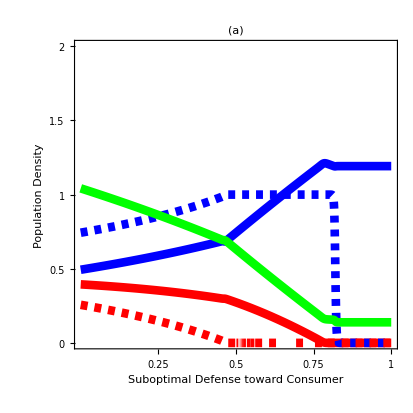

```mathematica
Fig7a = Show[Νfinalϕ,Pfinalϕ,eΝfinalϕ, ePfinalϕ,Rfinalϕ, Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer","Population Density", "","Defense Effort"}, ImageSize -> 414,Spacings-> 30,
PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2},
{0.5,1, 1.5, 2}},{{1, 0.75, 0.5, 0.25}, {None}}}]
```

```mathematica
Export["Figs/MoNSTR_Fig8_Full.tiff",Fig8,"TIFF", ImageResolution-> 600]
```

```mathematica
(*coexistence via increased novelty*)
```

```mathematica
parsFacNϕ = Delete[parsFacN, 14]
```

{r→1,k→0.28,c0→0.15,fP→0.8,aPR→0.9,aPΝ→1.5,aΝR→0.8,bPΝ→0.5,bΝR→1,bPR→0.5,mP→0.3,mΝ→0.1,v→1}

```mathematica
finalFacϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsFacNϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];
```

```mathematica
RfinalϕFac = Plot[Evaluate[R[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,0.28},{0,0.6}}];
ΝfinalϕFac = Plot[Evaluate[Ν[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,0.28},{0,0.6}}];
PfinalϕFac = Plot[Evaluate[P[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,0.28},{0,0.6}}];
eΝfinalϕFac = Plot[Evaluate[eΝ[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015],Blue, Dashed}, 
PlotRange->{{0,0.28},{0,0.6}}];
ePfinalϕFac = Plot[Evaluate[eP[ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Red, Dashed}, 
PlotRange->{{0,0.28},{0,0.6}}];
```

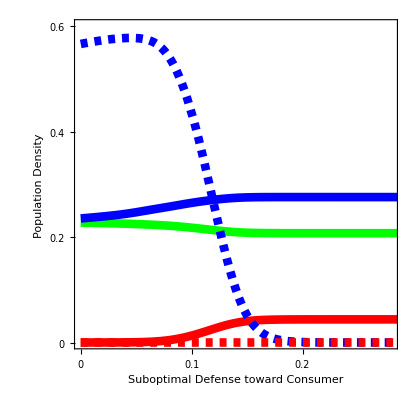

```mathematica
Fig8=Show[RfinalϕFac,ΝfinalϕFac,PfinalϕFac,eΝfinalϕFac, ePfinalϕFac, 
Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer","Population Density", "","Defense Effort"}, ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.2,0.4, 0.6},
{0,0.2,0.4, 0.6}},{{0, 0.1, 0.2}, {None}}}]
```

```mathematica
(* Export["Figs/MoNSTR_Fig8_Full.tiff",Fig8,"TIFF", ImageResolution-> 600] *)
```

```mathematica
Export["Figs/MoNSTR_Fig8_Full.pdf",Fig8]
```

### PLot final densities across a range of c0

```mathematica
c0parsϕH = {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
c0parsϕM =  {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->.75};
c0parsϕL =  {r-> 1,k-> 2.5, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->.5};
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

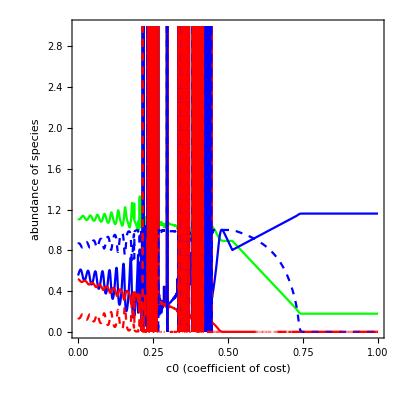

```mathematica
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

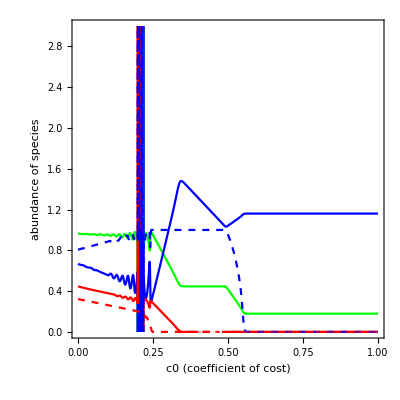

```mathematica
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

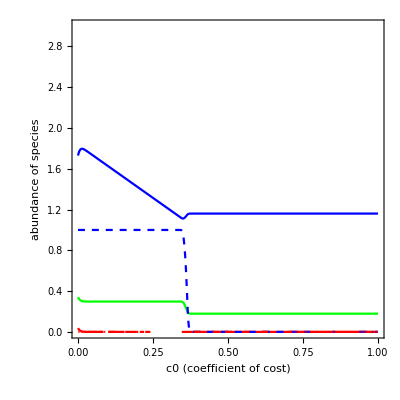

```mathematica
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

Determine equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→0 | Ν→0 | P→0 | eP→1-eΝ | 
R→-(c0-1) k r | Ν→0 | P→0 | eP→1-eΝ | 
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→(k (aΝR mP (fP ϕ-1)+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR mP (fP ϕ-1)+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (fP ϕ-1) (aΝR bΝR mP (fP ϕ-1)-aPΝ bΝR bPΝ (c0-1) r+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→mΝ/(aΝR bΝR-aΝR bΝR fP ϕ) | Ν→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR^2 bΝR k (fP ϕ-1)^2) | P→0 | eΝ→1 | eP→0
R→-(k r (c0 ϕ+c0-fP ϕ))/(fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(c0 r)/(aPR fP) | eΝ→-(aPΝ c0 r ϕ+aPR (aΝR bΝR k r (c0 ϕ+c0-fP ϕ)+fP mΝ ϕ))/(aΝR aPR bΝR fP k r ϕ (fP ϕ-c0 (ϕ+1))) | eP→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0 ϕ+c0-fP ϕ)+fP mP ϕ))/(aΝR aPR bPR fP k r (fP ϕ-c0 (ϕ+1)))
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(aΝR bΝR c0 k r-aΝR bΝR k r+mΝ)/(aΝR bΝR c0 fP k r ϕ-aΝR bΝR fP k r ϕ) | eP→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR bΝR (c0-1) fP k r ϕ)
R→(k (ϕ (aΝR bΝR mP (-fP ϕ+ϕ+1)-aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ (-fP ϕ+ϕ+1)))/(aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2) | Ν→-(aΝR bΝR mP ϕ+aPR bPR (mΝ-aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)))/(aΝR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | P→(ϕ (aPR bPR (aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)-mΝ)-aΝR bΝR mP ϕ))/(aPR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | eΝ→(-aΝR aPΝ mP ϕ+aΝR aPR^2 bPR (fP-1) k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR (fP-1) ϕ-bΝR bPΝ))-aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1))) | eP→(aΝR aPΝ mP ϕ+aΝR aPR^2 bPR k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1) (fP ϕ-1)+aPΝ (c0-1) r (-bΝR bPΝ fP ϕ+bΝR bPΝ+bPR ϕ))+aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1)))
R→(aΝR fP mP ϕ-aPΝ bPΝ c0 r)/(aΝR aPR bPR fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0-fP ϕ)+fP mP ϕ))/(aΝR aPR^2 bPR fP k ϕ) | eΝ→((aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))/(aΝR aPR fP k ϕ)+(bPR (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ c0 r-aΝR fP mP ϕ))/(bΝR bPΝ) | eP→0
R→k r (1-c0/(fP ϕ)) | Ν→(c0 r)/(aΝR fP ϕ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fP k r ϕ)+1/(fP ϕ) | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fP v ϕ | eP v (c0 r-aΝR fP Ν ϕ) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsExc,2];
subparsM=Delete[parsExcM,2];
subparsL=Delete[parsExcL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq14RΝ=JRΝ/.equil[[14,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq16RΝ=JRΝ/.equil[[16,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq3RP=JRP/.equil[[3,All]]//FullSimplify;
Jeq7RP=JRP/.equil[[7,All]]//FullSimplify;
Jeq5RP=JRP/.equil[[5,All]]//FullSimplify;
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.subpars],#≥0&];
AllFeas7[k_]=AllTrue[Re[equil[[7,All,2]]/.subpars],#≥0&];
AllFeas14[k_]=AllTrue[Re[equil[[14,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];

AllFeas3M[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig14RΝ[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig16RΝ[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subpars]]]];

pReEig14RΝM[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig3RP[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subpars]]]];
pReEig7RP[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subpars]]]];
pReEig5RP[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subpars]]]];

pReEig3RPM[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

Produce Plots

```mathematica
kaPΝparsH = Delete[parsExc, {{2},{6}}];
kaPΝparsM = Delete[parsExcM, {{2},{6}}];
kaPΝparsL = Delete[parsExcL, {{2},{6}}];
```

```mathematica
RstarRN14 = equil[[14,1,2]];
NstarRN14= equil[[14,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN16 = equil[[16,1,2]];
NstarRN16= equil[[16,2,2]];
```

```mathematica
PinvRN14 = bPR aPR (1 -0*fP)RstarRN14  + aPN bPΝ NstarRN14 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN16 = bPR aPR (1 -0*fP)RstarRN16  + aPN bPΝ NstarRN16 - mP;
```

### High Efficiency

```mathematica
plotPinvRN14 = FullSimplify[Solve[PinvRN14==0,aPN]][[1,1,2]];
PinvRN14kaPN = plotPinvRN14/.kaPΝparsH;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN16 = FullSimplify[Solve[PinvRN16==0,aPN]][[1,1,2]];
PinvRN16kaPN = plotPinvRN16/.kaPΝparsH;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];
```

```mathematica
Rstar3 = equil[[3,1,2]];
Pstar3= equil[[3,3,2]];
Rstar7 = equil[[7,1,2]];
Pstar7= equil[[7,3,2]];
Rstar5 = equil[[5,1,2]];
Pstar5= equil[[5,3,2]];
```

```mathematica
Νinv3 = bΝR aΝR (1 -0*fΝ)Rstar3  - aPΝ Pstar3 - mΝ;
Νinv7 = bΝR aΝR (1 -0*fΝ)Rstar7  - aPΝ Pstar7 - mΝ;
Νinv5= bΝR aΝR (1 -0*fΝ)Rstar5 - aPΝ Pstar5 - mΝ;
```

```mathematica
plotΝinv3= FullSimplify[Solve[Νinv3==0,aPΝ]][[1,1,2]];
Νinv3kaPN = plotΝinv3/.kaPΝparsH;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.1112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White, AspectRatio -> 1/1, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

plotΝinv7= FullSimplify[Solve[Νinv7==0,aPΝ]][[1,1,2]];
Νinv7kaPN = plotΝinv7/.kaPΝparsH;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

plotΝinv5= FullSimplify[Solve[Νinv5==0,aPΝ]][[1,1,2]];
Νinv5kaPN = plotΝinv5/.kaPΝparsH;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

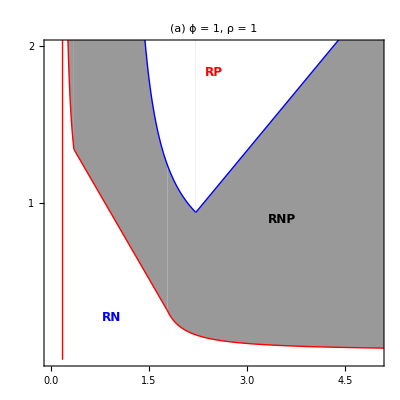

```mathematica
Fig5a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.2,0.15}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsM;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsM;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3kaPN = plotΝinv3/.kaPΝparsM;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig3RPM[x]< 0&&AllFeas3M[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsM;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsM;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

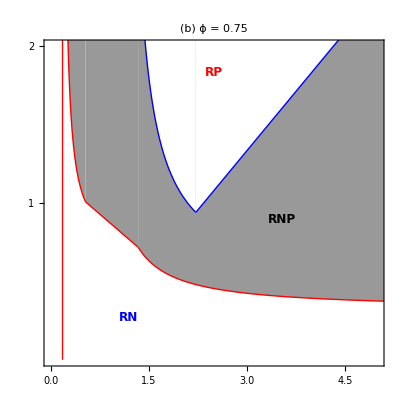

```mathematica
Fig5b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsL;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,1.112}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 1.112,1.85}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsL;
PlotRN16 = Plot[PinvRN16kaPN,{k, 1.85,6}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

Νinv3kaPN = plotΝinv3/.kaPΝparsL;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White,AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig3RPL[x]< 0&&AllFeas3L[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsL;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsL;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

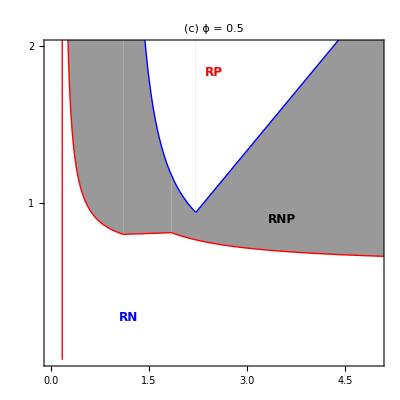

```mathematica
Fig5c= Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

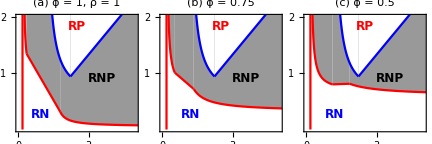
-Graphics-productivity (k)IGP strength

```mathematica
Figure5abc = Panel[GraphicsRow[{Fig5a,Fig5b,Fig5c}, ImageSize-> 432, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

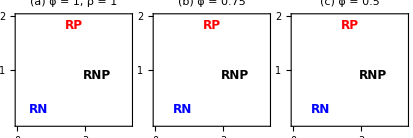
-Graphics-productivity (k)IGP strength

```mathematica
Figure5abcDIS = Panel[GraphicsRow[{Fig5a,Fig5b,Fig5c}, ImageSize-> 414, Spacings->0], {"productivity (k)",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White]
```

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
parsGood =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 1};
parsGoodM =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 0.75};
parsGoodL =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 0.5};
```

```mathematica
subpars=Delete[parsExc,3];
subparsM=Delete[parsExcM,3];
subparsL=Delete[parsExcL,3];
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas5[c0_]=AllTrue[Re[equil[[5,All,2]]/.subpars],#≥0&];
AllFeas7[c0_]=AllTrue[Re[equil[[7,All,2]]/.subpars],#≥0&];
AllFeas14[c0_]=AllTrue[Re[equil[[14,All,2]]/.subpars],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];

AllFeas3M[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];

pReEig14RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subpars]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig16RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subpars]]]];

pReEig14RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
pReEig3RP[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subpars]]]];
pReEig7RP[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subpars]]]];
pReEig5RP[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subpars]]]];

pReEig3RPM[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsExc, {{3},{6}}];
c0aPΝparsM = Delete[parsExcM, {{3},{6}}];
c0aPΝparsL = Delete[parsExcL, {{3},{6}}];
```

#### High relative efficiency (ϕ = 1)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsH;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsH;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsH;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsH;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsH;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

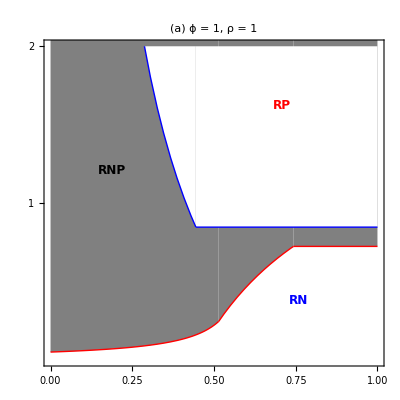

```mathematica
Fig6a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsM;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsM;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsM;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPM[x]<0&&AllFeas3M[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsM;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsM;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

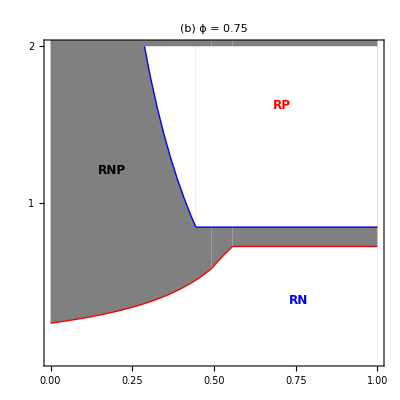

```mathematica
Fig6b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsL;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0.34,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsL;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,0.35}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝL[x]<0&&AllFeas16L[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsL;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPL[x]<0&&AllFeas3L[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsL;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsL;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

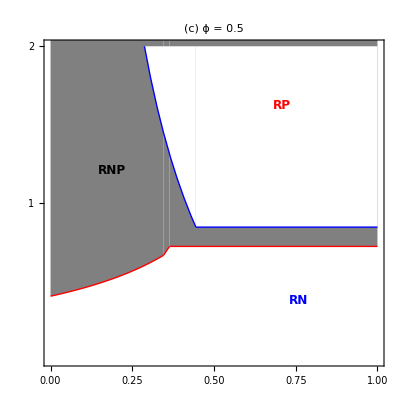

```mathematica
Fig6c =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

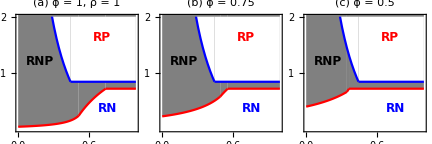
-Graphics-Defense CostIGP Strenght

```mathematica
Figure6abc = Panel[GraphicsRow[{Fig6a,Fig6b,Fig6c}, ImageSize-> 432, Spacings->0], {"Defense Cost",Rotate["IGP Strenght",Pi/2]},{Bottom,Left},Background->White]
```

## Introduced Intermediate Consumer (N): naivete toward Ν

Define Model: naïveté to Ν

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - (1-ρ) aΝR Ν (1- eΝ fΝ) - aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.2, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->.95};

parsCoex = {r-> 1,k-> 5, c0->0.25, fΝ->0.8, fP->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->.95};
parsExc = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->.95};
parsExcM = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->0.75};
parsExcL = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->0.5};

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ρ->1};
```

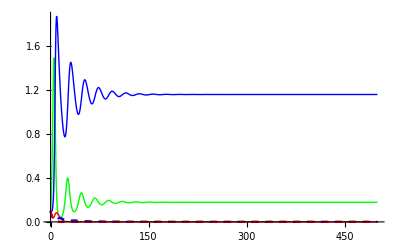

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExcL},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients of ρ

```mathematica
parsExcManips =Delete[parsExcL,{{3},{7}, {15}}];
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsExcManips,{c0 -> χ, aPΝ -> α, ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{χ,1,"c0"},0,1},{{α,1,"aPΝ"},0,2}, {{Ρ,0.5,"ρ"},0,1}]
```

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==-v eP[t] (Times[«4»]+Times[«4»]+Times[«4»]),eP[0]==0.1}}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]}.

ReplaceAll::reps: {{{R'[t]==R[t] (Times[«2»]+Times[«4»]+Times[«3»]+Times[«4»]),R[0]==0.1},{Ν'[t]==(Times[«2»]+Times[«3»]+Times[«4»]) Ν[t],Ν[0]==0.1},{P'[t]==P[t] (Times[«2»]+Times[«4»]+Times[«3»]),P[0]==0.1},{eΝ'[t]==v eΝ[t] (Times[«3»]+Times[«5»]+Times[«5»]),eΝ[0]==0.1},{eP'[t]==v eP[t] (Times[«3»]+Times[«5»]+Times[«5»]),eP[0]==0.1}}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsExcManips,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kparsρH = Delete[parsExc,2]
kparsρM = Delete[parsExcM,2]
kparsρL =Delete[parsExcL,2]
```

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.95}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.75}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.5}

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

$Aborted

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

$Aborted

$Aborted

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

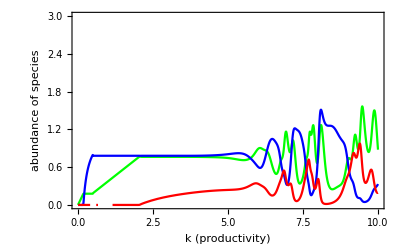

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

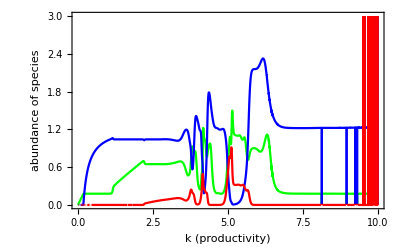

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

-Graphics-

### Final densities of RNP across naivete towards N (ρ)

```mathematica
parsStabρplot = {r-> 1,k-> 2.5, c0->0.4, fΝ->.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.55, mP->0.5, mΝ->0.1, v-> 1};
parsFacPρ = {r-> 1,k-> 0.7, c0->0.1, fΝ->.8,fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1};

parsGoodρ = {r-> 1,k-> 3, c0->0.1, fΝ->.6,fP->0.6,  aPR-> 1, aPΝ -> 0.8, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.4, mP->0.55, mΝ->0.1, v-> 1};
```

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsGoodρ},{R,Ν, P, eΝ, eP},{t,0,500}, {ρ}];
finalρR = Plot[Evaluate[R[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{0,1},{0,2}}];
finalρΝ = Plot[Evaluate[Ν[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Blue}, 
PlotRange->{{0,1},{0,2}}];
finalρP = Plot[Evaluate[P[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Red}, 
PlotRange->{{0,1},{0,2}}];
finalρeΝ = Plot[Evaluate[eΝ[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Dashed, Blue}, 
PlotRange->{{0,1},{0,2}}];
finalρeP = Plot[Evaluate[eP[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Dashed,  Red}, 
PlotRange->{{0,1},{0,2}}];
```

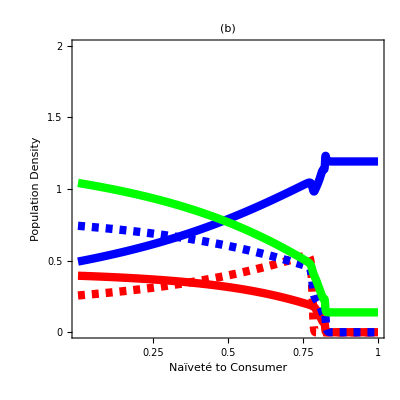

```mathematica
Fig7b = Show[ finalρP, finalρeP,finalρΝ,finalρeΝ,finalρR, Frame-> True, 
PlotLabel -> Style["(b)                                                                                       ", FontSize->14,  Bold],
FrameLabel->{"Naïveté to Consumer","Population Density", "","Defense Effort"},  
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, FrameTicks->{{{0,0.5,1, 1.5, 2},{0,0.5,1, 1.5, 2}},{{1, 0.75, 0.5,0.25}, {None}}}]
```

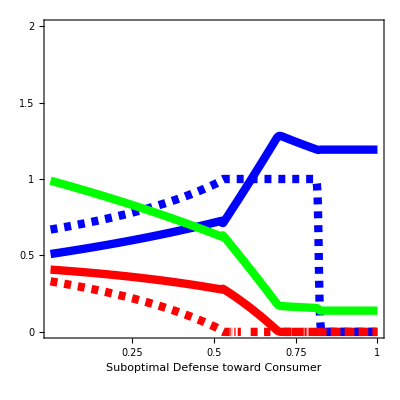

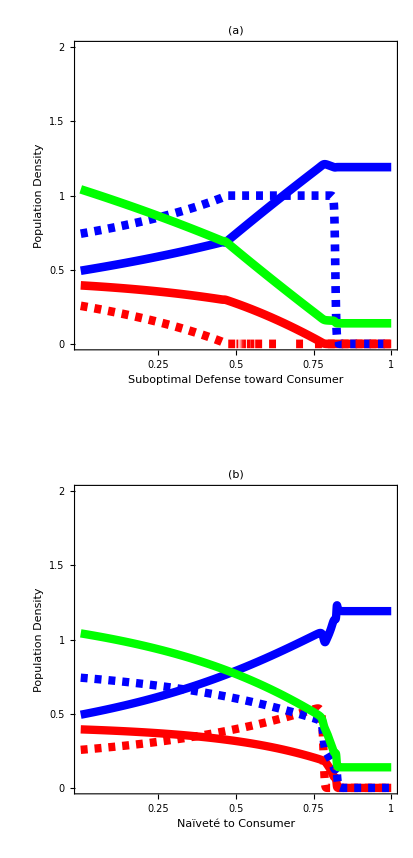
-Graphics-Novelty Gradient

```mathematica
Fig7ab =  Panel[GraphicsColumn[{Fig7a,Fig7b}, ImageSize-> 414, Spacings->{0,30}], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
```

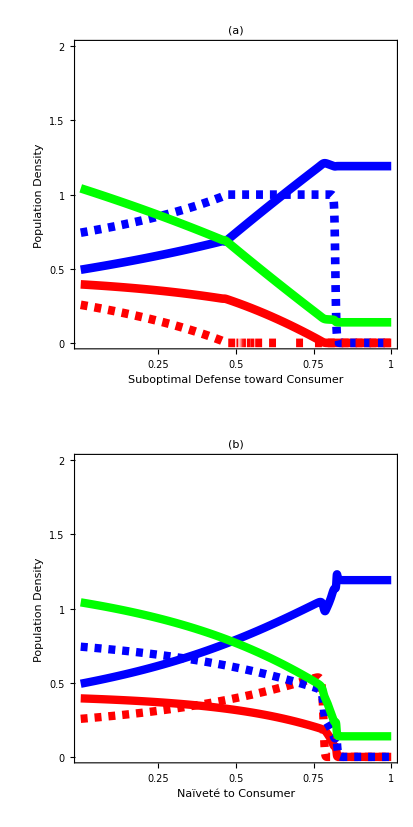
-Graphics-Novelty Gradient

```mathematica
Fig7ab =  Panel[GraphicsColumn[{Fig7a,Fig7b}, ImageSize-> 414, Spacings->0], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
```

```mathematica
(* Export["Figs/MoNSTR_Fig7_Full.tiff",Fig7ab,"TIFF", ImageResolution-> 600] *)
```

C:\Users\ingemank\Desktop\MoNSTR\Dissertation Figures\MoNSTR_Fig7_Full.tif

```mathematica
Export["Figs/MoNSTR_Fig7_Full.pdf",Fig7ab]
```

MoNSTR_Fig7_Full.pdf

Determine equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→-(c0-1) k r | Ν→0 | P→0 | eP→1-eΝ | 
R→0 | Ν→0 | P→0 | eP→1-eΝ | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP ρ-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(-aPΝ^2 bΝR bPΝ^2 c0^2 r^2+aΝR fΝ ρ (aPR bPR k r (aΝR bΝR mP ρ (fΝ-c0)+aPR bPR c0 mΝ (ρ-1))-aΝR bΝR fΝ mP^2 ρ)+aΝR aPΝ bΝR bPΝ c0 ρ r (aPR bPR k r (c0-fΝ)+2 fΝ mP))/(aΝR aPR^2 bPR fΝ k ρ (aΝR bΝR fΝ mP ρ+aPΝ c0 r (-bΝR bPΝ+bPR (-ρ)+bPR))) | eΝ→(aΝR fΝ ρ (aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))-aPΝ c0 r (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)))/(aΝR aPR fΝ k (aΝR bΝR fΝ mP ρ+aPΝ c0 r (-bΝR bPΝ+bPR (-ρ)+bPR))) | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→-(-(√k √r √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √ρ)+c0 k r-fΝ k r)/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→-((√ρ √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √k √r)-c0 (ρ-2)-fΝ ρ)/(2 c0 fΝ (ρ-1)) | eP→0
R→-((√k √r √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √ρ)+c0 k r-fΝ k r)/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→((√ρ √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √k √r)+c0 (ρ-2)+fΝ ρ)/(2 c0 fΝ (ρ-1)) | eP→0
R→(-aΝR aPR^2 bPR fP k mΝ ((fΝ-1) fP-fΝ) (bPΝ (bΝR-2 bΝR ρ)+bPR ρ)+(bΝR bPΝ-bPR ρ) √(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR fΝ k (aΝR bΝR mP ρ (fΝ (fP-1)-fP) (bΝR bPΝ+bPR (ρ-2))-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→(bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))+aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→-(ρ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))))/(2 aPΝ aPR fP (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ+2 fΝ (fP-1) ρ-(fΝ+1) fP)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fP (fΝ ρ+ρ-2)-fΝ ρ)-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (2 ρ-1)-fΝ fP+fP)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ ρ+(fΝ-1) fP (ρ-2))+aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(-aΝR aPR^2 bPR fP k mΝ ((fΝ-1) fP-fΝ) (bPΝ (bΝR-2 bΝR ρ)+bPR ρ)+(bPR ρ-bΝR bPΝ) √(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR fΝ k (aΝR bΝR mP ρ (fΝ (fP-1)-fP) (bΝR bPΝ+bPR (ρ-2))-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→(aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ)))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→-(ρ (bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))+aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)))/(2 aPΝ aPR fP (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ+2 fΝ (fP-1) ρ-(fΝ+1) fP)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fP (fΝ ρ+ρ-2)-fΝ ρ)-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (2 ρ-1)-fΝ fP+fP)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ ρ+(fΝ-1) fP (ρ-2))+aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))-aΝR aPR bΝR fΝ k ρ r (c0 (fΝ+fP)-fΝ fP))/(2 aΝR aPR bΝR fΝ^2 fP ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aΝR aPR bΝR fΝ k r (c0 (fP (ρ-2)-fΝ ρ)+fΝ fP ρ)-√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR c0 fΝ^2 fP k (ρ-1) r) | eP→(2 aΝR aPR^2 bPR c0 fΝ^2 fP k mΝ (ρ-1) ρ r+(aPΝ bPΝ c0 r-aΝR fΝ mP ρ) √(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))+aΝR aPR fΝ k ρ r (aPΝ c0 r (bΝR bPΝ (c0 (fΝ+fP)-fΝ fP)+2 bPR c0 fΝ (ρ-1))-aΝR bΝR fΝ mP ρ (c0 (fΝ+fP)-fΝ fP)))/(2 aΝR aPR bPR c0 fΝ^2 fP k (ρ-1) ρ r (aPΝ c0 r+aPR fP mΝ))
R→-(aΝR aPR bΝR fΝ k ρ r (c0 (fΝ+fP)-fΝ fP)+√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR fΝ^2 fP ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aΝR aPR bΝR fΝ k r (c0 (fP (ρ-2)-fΝ ρ)+fΝ fP ρ)+√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR c0 fΝ^2 fP k (ρ-1) r) | eP→(2 aΝR aPR^2 bPR c0 fΝ^2 fP k mΝ (ρ-1) ρ r+(aΝR fΝ mP ρ-aPΝ bPΝ c0 r) √(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))+aΝR aPR fΝ k ρ r (aPΝ c0 r (bΝR bPΝ (c0 (fΝ+fP)-fΝ fP)+2 bPR c0 fΝ (ρ-1))-aΝR bΝR fΝ mP ρ (c0 (fΝ+fP)-fΝ fP)))/(2 aΝR aPR bPR c0 fΝ^2 fP k (ρ-1) ρ r (aPΝ c0 r+aPR fP mΝ))
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fΝ ρ v | v (aΝR (1-2 eΝ) fΝ Ν ρ-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fΝ ρ v | eP v (c0 r-aΝR fΝ Ν ρ) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν ρ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R
0 | -aΝR (eΝ-1) eΝ fΝ ρ v | v (aΝR (1-2 eΝ) fΝ Ν ρ-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν ρ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsExc,2];
subparsM=Delete[parsExcM,2];
subparsL=Delete[parsExcL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq13RΝ=JRΝ/.equil[[13,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas8[k_]=AllTrue[Re[equil[[8,All,2]]/.subpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas13[k_]=AllTrue[Re[equil[[13,All,2]]/.subpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas13M[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas13L[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]];pReEig13RΝ[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subpars]]]];

pReEig13RΝM[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];
pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]];

pReEig13RΝL[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsL]]]] ;
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];
pReEig8RP[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subpars]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];
pReEig8RPM[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
pReEig8RPL[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsExc, {{2},{7}}];
kaPΝparsM = Delete[parsExcM, {{2},{7}}];
kaPΝparsL = Delete[parsExcL, {{2},{7}}];
```

#### new

```mathematica
RstarRN13 = equil[[13,1,2]];
NstarRN13= equil[[13,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN13 = bPR aPR (1 -0*fP)RstarRN13  + aPN bPΝ NstarRN13 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13kaPN = plotPinvRN13/.kaPΝparsH;
PlotRN13 = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig13RΝ[x]<0&&AllFeas13[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,2.45}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
Rstar8 = equil[[8,1,2]];
Pstar8= equil[[8,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv10 = bΝR aΝR (1 -0*fΝ)Rstar10  - aPΝ Pstar10 - mΝ;
Νinv8= bΝR aΝR (1 -0*fΝ)Rstar8 - aPΝ Pstar8 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8kaPN = plotΝinv8/.kaPΝparsH;
PlotRP8 = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

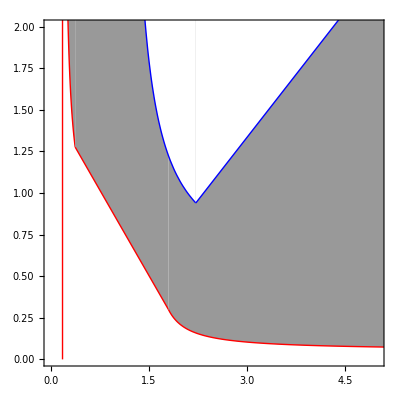

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Fig5aa = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},LabelStyle-> Larger]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsM;
PlotRN13M = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig13RΝM[x]<0&&AllFeas13M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19M = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17M = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6M = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10M = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsM;
PlotRP8M = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

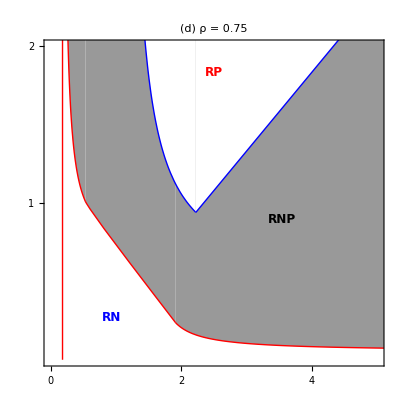

```mathematica
Fig5d =Show[PlotRN13M, PlotRN19M,PlotRN17M,PlotRP6M,PlotRP10M, PlotRP8M, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.2,0.15}]]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{0,2,4}, {None}}}]
```

#### Low relative efficiency (ϕ = 0.5)

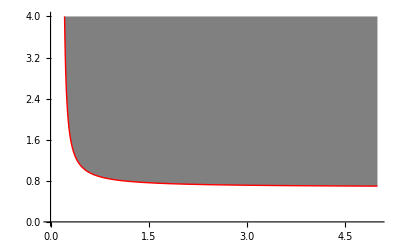

2.98807 (0.334664 (0.8-0.18 k)-0.284605 √(0.5 (0.0896 k+0.128)-0.128) √k)

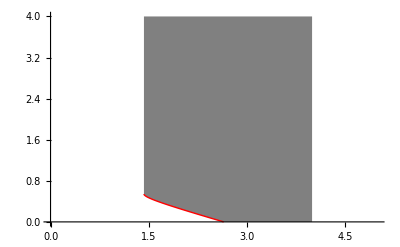

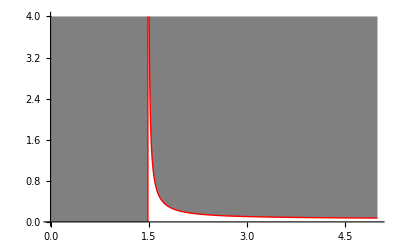

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsL;
PlotRN13L = Plot[PinvRN13kaPN,{k, 0.2,5},  PlotRange->{{0,5},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝL[x]<0&&AllFeas13L[x]]]

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL
PlotRN19L = Plot[PinvRN19kaPN,{k, 0,4}, PlotRange->{{0,5},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5]]

PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17L = Plot[PinvRN17kaPN,{k, 0,5}, PlotRange->{{0,5},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5]]

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k,  1.112,5}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig6RPL[x]<0&&AllFeas6L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,5}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsL;
PlotRP8L =PlotRP8L = Plot[Νinv8kaPN,{k, 0,5}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];
```

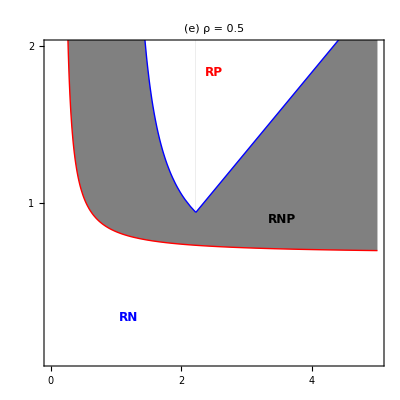

```mathematica
Fig5e =Show[PlotRN13L, PlotRP6L,PlotRP10L, PlotRP8L, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{1, 2},{None}},{{0,2, 4}, {None}}}]
```

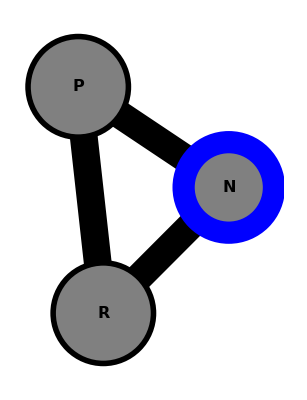

```mathematica
igpN=
Show[
Graphics[{{GrayLevel[0],Thickness[0.05],
Line[{{0.1, 0.1},{.6,.6}}], 
Line[{{0.6, 0.6},{0,1}}], 
Line[{{0.1, 0.1},{0,1}}] 
}}],
Graphics[{{GrayLevel[0.5],Disk[{.1,.1},.2]},{GrayLevel[0.5], Disk[{.6,.6},.2]}, {GrayLevel[0.5],Disk[{0,1.0},.2]}, {Blue,Thickness[0.04],Circle[{0.6,0.6},.18]}, 
{Black,Thickness[0.01],Circle[{0.1,0.1},.2]}, 
{Black,Thickness[0.01],Circle[{0,1},.2]}}],
Graphics[{Text[Style["R",16,Black , Bold],{0.1,0.1}], 
Text[Style["N",16,Black , Bold],{0.6,0.6}],
Text[Style["P",16,Black , Bold],{0,1}]}]]
```

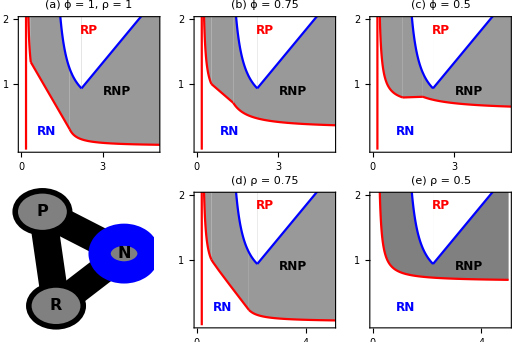
-Graphics-ProductivityIGP strength

```mathematica
Figure5abcde = Panel[GraphicsGrid[{{Fig5a,Fig5b, Fig5c},{igpN, Fig5d, Fig5e}}, ImageSize-> 518, Spacings->{20,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

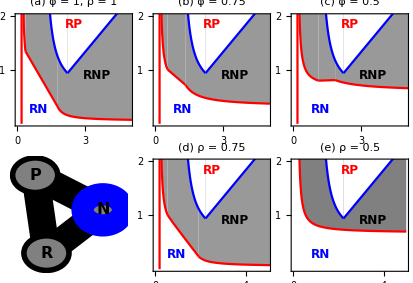
-Graphics-ProductivityIGP strength

```mathematica
Figure5abcdeDIS = Panel[GraphicsGrid[{{Fig5a,Fig5b, Fig5c},{igpN, Fig5d, Fig5e}}, ImageSize-> 414, Spacings->{0,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

```mathematica
(* Export["Figs/MoNSTR_Fig5_Full.tiff",Figure5abcdeDIS,"TIFF", ImageResolution->600] *)
```

```mathematica
Export["Figs/MoNSTR_Fig5_Full.pdf", Figure5abcde]
```

MoNSTR_Fig5_Full.pdf

### Invasibility Plot (c0 and aPN)

### Functions for working with equilibrium values across a gradient of cost (c0)

```mathematica
subpars=Delete[parsExc,3];
subparsM=Delete[parsExcM,3];
subparsL=Delete[parsExcL,3];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq13RΝ=JRΝ/.equil[[13,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[c0_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas8[c0_]=AllTrue[Re[equil[[8,All,2]]/.subpars],#≥0&];
AllFeas10[c0_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas13[c0_]=AllTrue[Re[equil[[13,All,2]]/.subpars],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];

AllFeas6M[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[c0_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas10M[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas13M[c0_]=AllTrue[Re[equil[[13,All,2]]/.subparsM],#≥0&];
AllFeas17M[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];

AllFeas6L[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[c0_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas10L[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas13L[c0_]=AllTrue[Re[equil[[13,All,2]]/.subparsL],#≥0&];
AllFeas17L[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]];pReEig13RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subpars]]]];

pReEig13RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsM]]]];
pReEig19RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];
pReEig17RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]];

pReEig13RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsL]]]] ;
pReEig19RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
pReEig17RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig10RP[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];
pReEig8RP[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subpars]]]];

pReEig6RPM[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig10RPM[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];
pReEig8RPM[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig10RPL[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
pReEig8RPL[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

#### P invades RN

```mathematica
c0aPΝparsH = Delete[parsExc, {{3},{7}}]
c0aPΝparsM = Delete[parsExcM, {{3},{7}}];
c0aPΝparsL = Delete[parsExcL, {{3},{7}}];
```

{r→1,k→2.5,fΝ→0.8,fP→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.95}

#### High Recognition (ρ = 1)

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsH;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝ[x]<0&&AllFeas13[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsH;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsH;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsH;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsH;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsH;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

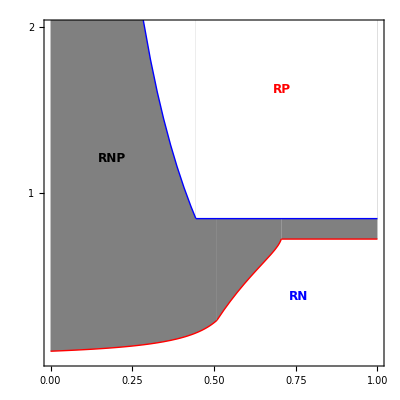

```mathematica
Fig6aa = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["", FontSize->12,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{None}, {None}}}]
```

#### Medium naivete (ρ = 0.75)

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsM;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝM[x]<0&&AllFeas13M[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsM;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,0.56}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsM;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,0.56}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsM;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsM;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsM;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

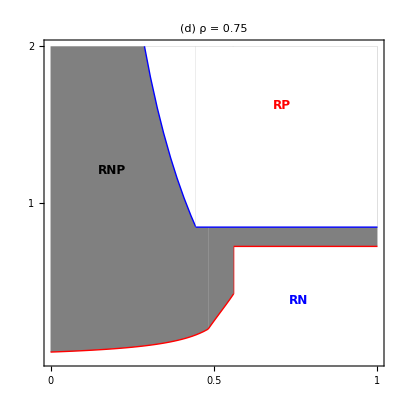

```mathematica
Fig6d = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
Graphics[{Red,Thick,
Line[{{0.56,0.72},{0.56,0.42}}]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{0,0.5, 1}, {None}}}]
```

#### Low recognition (ρ = 0.5)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsL;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsL;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsL;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];

plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsL;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝL[x]<0&&AllFeas13L[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsL;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,0.372}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsL;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,0.372}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];
```

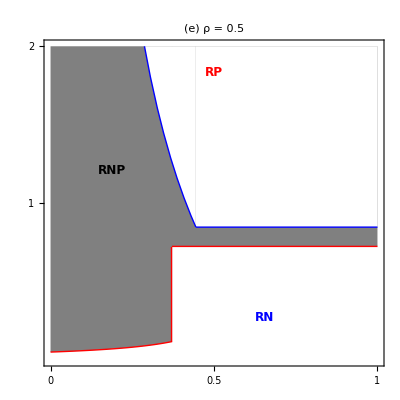

```mathematica
Fig6e =Show[ PlotRN19, PlotRN17, PlotRN13,PlotRP6,PlotRP10, PlotRP8, 
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.65,0.15}]]}],
Graphics[{Red,Thick,
Line[{{0.37,0.72},{0.37,0.115}}]}],
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{1, 2},{None}},{{0,0.5, 1}, {None}}}]
```

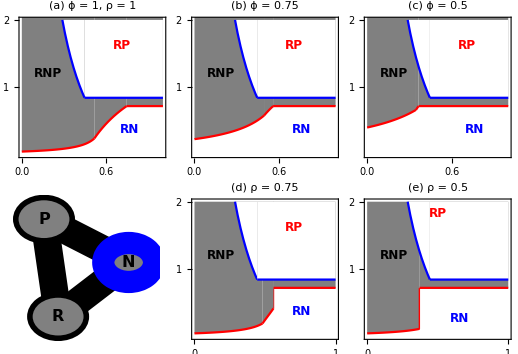
-Graphics-Defense CostIGP strength

```mathematica
Figure6abcde = Panel[GraphicsGrid[{{Fig6a,Fig6b, Fig6c},{igpN, Fig6d, Fig6e}}, ImageSize-> 518, Spacings->{0,20}], {"Defense Cost",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

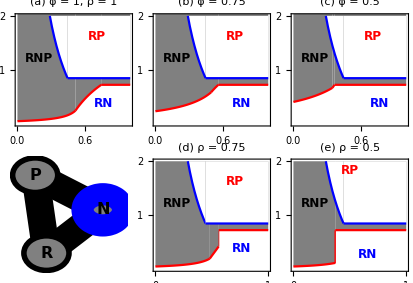
-Graphics-Defense CostIGP strength

```mathematica
Figure6abcdeDIS = Panel[GraphicsGrid[{{Fig6a,Fig6b, Fig6c},{igpN, Fig6d, Fig6e}}, ImageSize-> 414, Spacings->{0,20}], {"Defense Cost",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
```

```mathematica
(* Export["Figs/MoNSTR_Fig6_Full.tiff",Figure6abcdeDIS,"TIFF", ImageResolution->600] *)
```

```mathematica
Export["Figs/MoNSTR_Fig6_Full.pdf",Figure6abcde]
```

MoNSTR_Fig6_Full.pdf